# Parameter sweeps for the 1+1D switch model

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm.
We sweep kD, kdD, and μ to illustrate how standing and traveling waves in the phase diagram compared to the Denk et al. & extended skeleton parameters.

Parameters for the switch model inferred in this project

```mathematica
params={
rhoD->1000/4,
rhoE->1000/4,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3*4,
kdD->0.0015*4,
kdEr->1.5*4,
kdEl->10^-5*4,
kde->1,
λ->5,
μ->20,
L->50,
T->3000
};
```

Parameters for the extended switch model

```mathematica
paramsSkeletonSwitch={
rhoD->1000/4,
rhoE->1000/4,
DD->16,
DE->10,
Dd->0.013,
Dde->0.013,
kD->0.1*4,
kdD->0.108/2*4,
kdEr->0.435/2*10*4,
kdEl->0.435/2*10^-3*4,
kde->1.925,
λ->6,
μ->100,
L->50,
T->3000
};
```

Parameters for the in vitro switch model from Denk, et al., PNAS 2018;
To use these parameters in the in vivo setting: Use in vivo cytosolic diffusion coefficients.
In addition, the rate kde is changed to make the instability region more similar to the experimental diagram.

```mathematica
paramsDenkScaled={
rhoD->1000/4,
rhoE->1000/4,
DD->16,
DE->10,
Dd->0.013,
Dde->0.013,
kD->0.065*4,
kdD->0.02*4,
kdEr->0.02*10^2*4,
kdEl->0.02*10^-2*4,
kde->0.34*5,
λ->6,
μ->100,
L->50,
T->3000
};
```

## Setup

Setup the reaction terms for the 1+1D switch model

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

## 1+1D simulation

### PDE solver

The time for solving can be constraint to a maximal simulation time.

```mathematica
ClearAll@runMinSwitchSim;
(*set MaxSimulationTime to -1 to disable, otherwise maximal time allowed for NDSolve to execute in seconds*)
Options[runMinSwitchSim]=Join[Options[NDSolve],{"GridPoints"->200,"BC"->"Reflective","MaxSimulationTime"->200}];
runMinSwitchSim[f_,params_,{cDDInit_,cDTInit_,cErInit_,cElInit_,mdInit_,mdeInit_},tMax_,opts:OptionsPattern[]]:=If[OptionValue["MaxSimulationTime"]<=0,
First@NDSolve[{
D[cDD[x,t],t]==DD D[cDD[x,t],{x,2}]
+(f[[1]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cDT[x,t],t]==DD D[cDT[x,t],{x,2}]
+(f[[2]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cEr[x,t],t]==DE D[cEr[x,t],{x,2}]
+(f[[3]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cEl[x,t],t]==DE D[cEl[x,t],{x,2}]
+(f[[4]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[md[x,t],t]==Dd D[md[x,t],{x,2}]
+(f[[5]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[mde[x,t],t]==Dde D[mde[x,t],{x,2}]
+(f[[6]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
cDD[0,t]==cDD[L,t],(D[cDD[x,t],x]/.x->0)==(D[cDD[x,t],x]/.x->L),
cDT[0,t]==cDT[L,t],(D[cDT[x,t],x]/.x->0)==(D[cDT[x,t],x]/.x->L),
cEr[0,t]==cEr[L,t],(D[cEr[x,t],x]/.x->0)==(D[cEr[x,t],x]/.x->L),
cEl[0,t]==cEl[L,t],(D[cEl[x,t],x]/.x->0)==(D[cEl[x,t],x]/.x->L),
md[0,t]==md[L,t],(D[md[x,t],x]/.x->0)==(D[md[x,t],x]/.x->L),
mde[0,t]==mde[L,t],(D[mde[x,t],x]/.x->0)==(D[mde[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[cDD[x,t],x]/.x->0)==0,(D[cDD[x,t],x]/.x->L)==0,
(D[cDT[x,t],x]/.x->0)==0,(D[cDT[x,t],x]/.x->L)==0,
(D[cEr[x,t],x]/.x->0)==0,(D[cEr[x,t],x]/.x->L)==0,
(D[cEl[x,t],x]/.x->0)==0,(D[cEl[x,t],x]/.x->L)==0,
(D[md[x,t],x]/.x->0)==0,(D[md[x,t],x]/.x->L)==0,
(D[mde[x,t],x]/.x->0)==0,(D[mde[x,t],x]/.x->L)==0
}
],
(* initial condition *)
cDD[x,0]==cDDInit[x],
cDT[x,0]==cDTInit[x],
cEr[x,0]==cErInit[x],
cEl[x,0]==cElInit[x],
md[x,0]==mdInit[x],
mde[x,0]==mdeInit[x]
}/.params,
{cDD,cDT,cEr,cEl,md,mde},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
],
TimeConstrained[First@NDSolve[{
D[cDD[x,t],t]==DD D[cDD[x,t],{x,2}]
+(f[[1]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cDT[x,t],t]==DD D[cDT[x,t],{x,2}]
+(f[[2]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cEr[x,t],t]==DE D[cEr[x,t],{x,2}]
+(f[[3]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[cEl[x,t],t]==DE D[cEl[x,t],{x,2}]
+(f[[4]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[md[x,t],t]==Dd D[md[x,t],{x,2}]
+(f[[5]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
D[mde[x,t],t]==Dde D[mde[x,t],{x,2}]
+(f[[6]]/.{cDD->cDD[x,t],cDT->cDT[x,t],cEr->cEr[x,t],cEl->cEl[x,t],md->md[x,t],mde->mde[x,t],mede->mede[x,t],me->me[x,t]}),
If[OptionValue["BC"]==="Periodic",
{(* periodic BCs *)
cDD[0,t]==cDD[L,t],(D[cDD[x,t],x]/.x->0)==(D[cDD[x,t],x]/.x->L),
cDT[0,t]==cDT[L,t],(D[cDT[x,t],x]/.x->0)==(D[cDT[x,t],x]/.x->L),
cEr[0,t]==cEr[L,t],(D[cEr[x,t],x]/.x->0)==(D[cEr[x,t],x]/.x->L),
cEl[0,t]==cEl[L,t],(D[cEl[x,t],x]/.x->0)==(D[cEl[x,t],x]/.x->L),
md[0,t]==md[L,t],(D[md[x,t],x]/.x->0)==(D[md[x,t],x]/.x->L),
mde[0,t]==mde[L,t],(D[mde[x,t],x]/.x->0)==(D[mde[x,t],x]/.x->L)
},
{(* no-flux BCs *)
(D[cDD[x,t],x]/.x->0)==0,(D[cDD[x,t],x]/.x->L)==0,
(D[cDT[x,t],x]/.x->0)==0,(D[cDT[x,t],x]/.x->L)==0,
(D[cEr[x,t],x]/.x->0)==0,(D[cEr[x,t],x]/.x->L)==0,
(D[cEl[x,t],x]/.x->0)==0,(D[cEl[x,t],x]/.x->L)==0,
(D[md[x,t],x]/.x->0)==0,(D[md[x,t],x]/.x->L)==0,
(D[mde[x,t],x]/.x->0)==0,(D[mde[x,t],x]/.x->L)==0
}
],
(* initial condition *)
cDD[x,0]==cDDInit[x],
cDT[x,0]==cDTInit[x],
cEr[x,0]==cErInit[x],
cEl[x,0]==cElInit[x],
md[x,0]==mdInit[x],
mde[x,0]==mdeInit[x],
WhenEvent[TimeRemaining[]<OptionValue["MaxSimulationTime"],"StopIntegration","LocationMethod"->"StepBegin"]
}/.params,
{cDD,cDT,cEr,cEl,md,mde},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},(*Choose higher scale factor to enforce boundary conditions in case the initial condition does not fulfil them*)"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
],2OptionValue["MaxSimulationTime"]]
];
```

### Construction of the initial condition

```mathematica
SeedRandom[20220712];
iniRand=RandomReal[{-1,1},100].Table[Cos[i Pi #],{i,100}]&;
iniRand2=RandomReal[{-1,1},100].Table[Cos[i Pi #],{i,100}]&;
```

### hdf5 export function

Export simulation results to hdf5 files, one file for each phase diagram.

Set the file structure up.
data: association with keys corresponding to the different fields of the model

```mathematica
ClearAll[hdf5ExportSetup];
hdf5ExportSetup[filename_,params_,parameterNames_,parameterValues_,times_,grid_]:=Block[
{
sep={"/","=",",","="},
groups,
attr,
paramsAttr
},
groups=StringJoin[Riffle[sep,Riffle[parameterNames,ToString/@#]]]&/@parameterValues;
Export[filename,groups,"Groups"];
attr=Thread[groups->(Thread[parameterNames->#]&/@parameterValues)];
paramsAttr=Thread[(ToString/@params[[All,1]])->params[[All,2]]];
Export[filename,Join[{"/"->Join[{
"VariedParameters"->parameterNames,
"Model"->NotebookFileName[],
"Date"->DateString[],
"ExportedDomainDimension"->1,
"DatasetDimensions"->{Length@times,Length@grid}
},paramsAttr]},
attr],"Attributes",OverwriteTarget->"Append"];
Export[filename,{
"ValuesVariedParameters"->parameterValues,
"Times"->times,
"Grid"->grid
},"Datasets",OverwriteTarget->"Append"];
];
```

Fill in a full phase diagram

```mathematica
ClearAll[hdf5ExportParameterGroup];
Options[hdf5ExportParameterGroup]={"Attributes"->{}};
hdf5ExportParameterGroup[filename_,parameterNames_,variedParams_,data_,times_,opts:OptionsPattern[]]:=Block[
{
sep={"/","=",",","="},
group,
datasets,
timesteps,
endtime
},
group=StringJoin[Riffle[sep,Riffle[parameterNames,ToString/@variedParams]]];
If[data===-1||data===-2,
Export[filename,{group->{"Failed"->1}},"Attributes",OverwriteTarget->"Append"];,
datasets=group<>"/"<>#&/@Keys@data;
timesteps=Length[Values[data][[1]]];
endtime=times[[timesteps]];
Export[filename,Thread[datasets->Values@data],"Datasets",OverwriteTarget->"Append"];
Export[filename,{group->Join[{"Failed"->0,"Endtime"->endtime,"TimeSteps"->timesteps},OptionValue["Attributes"]]},"Attributes",OverwriteTarget->"Append"];
]
];
```

Save each simulation for a rhoD-rhoE concentration combination in an individual hdf5 file

```mathematica
ClearAll[hdf5ExportParameterGroupIndepFiles];
Options[hdf5ExportParameterGroupIndepFiles]={"Attributes"->{}};
hdf5ExportParameterGroupIndepFiles[filename_,parameterNames_,variedParams_,data_,times_,opts:OptionsPattern[]]:=Block[
{
sep={"/","=",",","="},
group,
tempfilename,
datasets,
timesteps,
endtime
},
group=StringJoin[Riffle[sep,Riffle[parameterNames,ToString/@variedParams]]];
tempfilename=StringReplace[filename,".h5"->""]<>StringReplace[group,{"/"->"","."->"_",","->"_"}]<>".h5";
Export[tempfilename,{group},"Groups"];
If[data===-1||data===-2,
Export[tempfilename,{group->{"Failed"->1}},"Attributes",OverwriteTarget->"Append"];,
datasets=group<>"/"<>#&/@Keys@data;
timesteps=Length[Values[data][[1]]];
endtime=times[[timesteps]];
Export[tempfilename,Thread[datasets->Values@data],"Datasets",OverwriteTarget->"Append"];
Export[tempfilename,{group->Join[{"Failed"->0,"Endtime"->endtime,"TimeSteps"->timesteps},OptionValue["Attributes"]]},"Attributes",OverwriteTarget->"Append"];
]
];
```

```mathematica
ClearAll[hdf5ExportParameterGroupIndepFilesTA];
Options[hdf5ExportParameterGroupIndepFilesTA]={"Attributes"->{}};
hdf5ExportParameterGroupIndepFilesTA[filename_,parameterNames_,variedParams_,data_,opts:OptionsPattern[]]:=Block[
{
sep={"/","=",",","="},
group,
tempfilename,
datasets,
timesteps,
endtime
},
group=StringJoin[Riffle[sep,Riffle[parameterNames,ToString/@variedParams]]];
tempfilename=StringReplace[filename,".h5"->""]<>StringReplace[group,{"/"->"","."->"_",","->"_"}]<>".h5";
Export[tempfilename,{group},"Groups"];
If[data===-1||data===-2,
Export[tempfilename,{group->{"Failed"->1}},"Attributes",OverwriteTarget->"Append"];,
datasets=group<>"/"<>#&/@Keys@data;
timesteps=Length[Values[data][[1]]];
endtime=data["Times"][[-1]];
Export[tempfilename,Thread[datasets->Values@data],"Datasets",OverwriteTarget->"Append"];
Export[tempfilename,{group->Join[{"Failed"->0,"Endtime"->endtime,"TimeSteps"->timesteps},OptionValue["Attributes"]]},"Attributes",OverwriteTarget->"Append"];
]
];
```

Combine all the individual files into a single file for a phase diagram, previously set up by hdf5ExportSetup

```mathematica
ClearAll[hdf5ExportCombine];
hdf5ExportCombine[filename_,parameterNames_,parameterValues_]:=Block[
{
sep={"/","=",",","="},
groups,
tempfilename,
data,
attrs
},
groups=StringJoin[Riffle[sep,Riffle[parameterNames,ToString/@#]]]&/@parameterValues;
Do[
tempfilename=StringReplace[filename,".h5"->""]<>StringReplace[group,{"/"->"","."->"_",","->"_"}]<>".h5";
data=Import[tempfilename,group];
attrs=Import[tempfilename,{"Attributes",group}];
Export[filename,Thread[((group<>"/"<>#&/@Keys@#)->Values@#)&@data],"Datasets",OverwriteTarget->"Append"];
Export[filename,{group->(attrs/.Association->List)},"Attributes",OverwriteTarget->"Append"];
DeleteFile[tempfilename];,
{group,groups}];
];
```

### Number format for filenames

```mathematica
ClearAll[toString];
toString[n_]:=ToString@ScientificForm[N@n,NumberFormat->(If[#3!="",ToString[Round@ToExpression@#1]<>"e"<>#3,ToString[Round@ToExpression@#1]]&)];
```

### Pattern simulation

...TA stresses that the endtime until which the dynamics is solved is adaptive: The simulation is terminated earlier if it takes too much time.

```mathematica
ClearAll[simPatternsTA];
Options[simPatternsTA]=Options[runMinSwitchSim];
simPatternsTA[params_,HSS_,times_,grid_,opts:OptionsPattern[]]:=Block[{
sim,
endtime=T/.params,
dt,
data,ps,psMax,period,
sim2,endtime2,
evalTimes=times
},

sim=Quiet[runMinSwitchSim[f,
params,
Thread[Evaluate[(1+{0,0,0,0,0.01iniRand[#/L],0.01iniRand2[#/L]})*HSS]&],
T/.params,Sequence@@(List@opts)]];
endtime=Quiet@Check[(md/.sim)["Domain"][[2,2]],I];
If[endtime==I,
Print["simulation failed at params = ",params];
Return[-1];];(*simulation failed*)

dt=Mean@Differences[(md/.sim)["Coordinates"][[2]]];
data=Table[md[x,t]+mde[x,t]/.sim,{x,Range[1/40,1,1/20]*L/.params},{t,Range[9endtime/10,endtime,dt]}];
ps=Mean[Abs[Fourier@(#-Mean@#)]^2&/@data];
psMax=SortBy[Transpose@{2Pi /Length[ps]*(Range[Length@ps]-1),ps},#[[2]]&][[-1]];
period=Quiet[Check[dt 2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],endtime/10,Power::infy],Power::infy];

(*account for shortend solution time*)
If[endtime<(T/.params),

If[endtime>100period,

evalTimes=Range[0,endtime,period/50];,

Print["Prolong simulation because less than 100 periods were simulated and the max time T=",T/.params," was not reached."];
sim2=Quiet[runMinSwitchSim[f,
params,
{(cDD[#,endtime]/.sim)&,(cDT[#,endtime]/.sim)&,(cEr[#,endtime]/.sim)&,(cEl[#,endtime]/.sim)&,(md[#,endtime]/.sim)&,(mde[#,endtime]/.sim)&},
200period-endtime,
Sequence@@Join[{"MaxSimulationTime"->1000},DeleteCases[List@opts,"MaxSimulationTime"->_]]]];
endtime2=Quiet@Check[(md/.sim2)["Domain"][[2,2]],I];
If[endtime2==I,
Print["simulation failed at params = ",params];
Return[-1];];(*simulation failed*)
If[endtime2<100period-endtime,
Print["solution took to long and was only computed until ",endtime+endtime2," for the parameters ", params,", which corresponds to roughly ",Round[(endtime+endtime2)/period]," periods."];];
evalTimes=Range[0,endtime+endtime2,period/50];
Return[<|
"cDD"->Table[If[t<endtime,cDD[x,t]/.sim,cDD[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"cDT"->Table[If[t<endtime,cDT[x,t]/.sim,cDT[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"cEr"->Table[If[t<endtime,cEr[x,t]/.sim,cEr[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"cEl"->Table[If[t<endtime,cEl[x,t]/.sim,cEl[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"md"->Table[If[t<endtime,md[x,t]/.sim,md[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"mde"->Table[If[t<endtime,mde[x,t]/.sim,mde[x,t-endtime]/.sim2],{t,evalTimes},{x,grid}],
"Times"->evalTimes,
"Period"->period
|>]
];
];
<|
"cDD"->Table[cDD[x,t]/.sim,{t,evalTimes},{x,grid}],
"cDT"->Table[cDT[x,t]/.sim,{t,evalTimes},{x,grid}],
"cEr"->Table[cEr[x,t]/.sim,{t,evalTimes},{x,grid}],
"cEl"->Table[cEl[x,t]/.sim,{t,evalTimes},{x,grid}],
"md"->Table[md[x,t]/.sim,{t,evalTimes},{x,grid}],
"mde"->Table[mde[x,t]/.sim,{t,evalTimes},{x,grid}],
"Times"->evalTimes,
"Period"->period
|>
];
```

### Pattern simulation sweep

Simulate one phase diagram, using parallel kernels

```mathematica
ClearAll[simSweepTA];
(*set FinerGridIfFailed to -1 to disable feature*)
Options[simSweepTA]=Join[Options[runMinSwitchSim],{"FinerGridIfFailed"->(("GridPoints"/.Options[runMinSwitchSim])*2),"TIni"->0}];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
simSweepTA[filename_,params_,variedParams_,dt_,dx_,opts:OptionsPattern[]]:=Block[{
parameterNames=ToString[#[[1]]]&/@variedParams,
variedParamComs=Flatten[Outer[List,Sequence@@(variedParams[[All,2]])],Length[variedParams]-1],
times=Range[OptionValue["TIni"],T/.params,dt],
grid=Range[dx/2,L/.params,dx],
sim
},
hdf5ExportSetup[filename,params,parameterNames,variedParamComs,times,grid];

ParallelDo[Block[{
ps=Join[Thread[variedParams[[All,1]]->vps],DeleteCases[params,Alternatives[Sequence@@((#[[1]]->_)&/@variedParams)]]],
instab
},
PrintTemporary[vps];
instab=Quiet@Check[testInstab[ps],I];
If[instab==I||Length[instab[[-1]]]<1,
Print["No hss found."];
hdf5ExportParameterGroupIndepFiles[filename,parameterNames,vps,-1,times];
Continue[];
];
sim=simPatternsTA[ps,instab[[-1]],times,grid,Evaluate[Sequence@@FilterRules[List@opts,Options[simPatternsTA]]]];
If[sim===-1&&OptionValue["FinerGridIfFailed"]>0,
Print["Simulation failed. Increase gridpoints to ",OptionValue["FinerGridIfFailed"]," and try again."];
sim=simPatternsTA[ps,instab[[-1]],times,grid,Sequence@@(Join[{"GridPoints"->OptionValue["FinerGridIfFailed"],"MaxSimulationTime"->1000},DeleteCases[List@opts,("GridPoints"->_)|("FinerGridIfFailed"->_)]])];
];
hdf5ExportParameterGroupIndepFilesTA[filename,parameterNames,vps,DeleteCases[sim/.Association->List,"Period"->_],"Attributes"->{"Period"->sim["Period"]}];
],{vps,variedParamComs},"Method"->"FinestGrained"];

hdf5ExportCombine[filename,parameterNames,variedParamComs];
];
```

### Pattern test

Classify patterns based on the morphological analysis of the pattern kymograph

```mathematica
ClearAll[testPatternMorphological];
Options[testPatternMorphological] = {"TimePoints" -> 200, "BoundaryPoints" -> 1};
testPatternMorphological[kymo_, opts : OptionsPattern[]] := Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,
morphComp,
nHighDensClusters
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

If[(max-min)/min < 0.05,
{I,0},(*no pattern formation*)
psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

If[period>Min[OptionValue["TimePoints"],Length@kymo]/2,
{2I,0},(*too short time window*)

morphComp=MorphologicalComponents[Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,

Print[Colorize@MorphologicalComponents[Binarize@Image@kymo[[-Min[1000,Length@kymo];;;;10,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"];;4]]]];
Print["period: ",N@period,", wavelength: ",N@wavelength];

morphComp=MorphologicalComponents[ColorNegate@Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,
{5I,relContrast},
Print["inverted SW"];
{4I,relContrast}(*inverted SWs*)
],(*TWs*)

{6I,relContrast}(*SWs*)
]
]
]
];
```

### Pattern test sweep

```mathematica
ClearAll[testSweepMorph];
Options[testSweepMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMorph[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}],
sep={"/","=",",","="}
},
Reap[
Do[Block[{
group=StringJoin[Riffle[sep,Riffle[parameterNames,{ToString@vps[[1]],ToString[vps[[2]]]}]]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/md",group<>"/mde"}}]]];
If[!MatrixQ[data],Print["No data at ",vps,", params: kD = ",Import[filename,{"Attributes","/"}]["kD"]," and kdD = ",Import[filename,{"Attributes","/"}]["kdD"]];Continue[]];
analysis=testPatternMorphological[data,Sequence@@(List@opts)];
If[analysis[[1]]==5I||analysis[[1]]==4I,Print[Log10@vps];];
Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[testSweepMultipleFilesMorph];
Options[testSweepMultipleFilesMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMultipleFilesMorph[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@testSweepMorph[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

### Plot pattern kymograph

```mathematica
ClearAll[dataKymo];
(*valuesVariedParameters is one parameter set here*)
dataKymo[filenameList_,valuesVariedParameters_]:=Block[{
kymo,
sep={"/","=",",","="}
},
Reap[Do[
Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
group
},
group=StringJoin[Riffle[sep,Riffle[parameterNames,StringTrim[#,"0"...]&/@{ToString@SetPrecision[#[[1]],6],ToString@SetPrecision[#[[2]],6]}&@Evaluate[valuesVariedParameters]]]];
Print[group];

If[MemberQ[Import[filename,"Datasets"],group<>"/md"],
Sow[Import[filename,{{group<>"/md",group<>"/mde"}}]]];
],
{filename,filenameList}];][[-1,1,1]]
];
```

### Wavelength & period analysis

```mathematica
ClearAll[analyzeKymo];
Options[analyzeKymo]={"TimePoints"->200,"BoundaryPoints"->25,"DX"->0.5,"DT"->4};
analyzeKymo[kymo_,opts:OptionsPattern[]]:=Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,
dx=OptionValue["DX"],
dt=OptionValue["DT"]
},

testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

If[(max-min)/min < 0.05,
I,

psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=dx Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=dt Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

{
relContrast,
wavelength,
period
}
]
];
```

```mathematica
ClearAll[analysisSweep];
Options[analysisSweep]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweep[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}],
sep={"/","=",",","="}
},

Reap[
Do[Block[{
group=StringJoin[Riffle[sep,Riffle[parameterNames,{ToString@vps[[1]],ToString[vps[[2]]]}]]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/md",group<>"/mde"}}]]];
If[!MatrixQ[data],Continue[]];
analysis=analyzeKymo[data,Sequence@@(List@opts)];

Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[analysisSweepMultipleFiles];
Options[analysisSweepMultipleFiles]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweepMultipleFiles[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@analysisSweep[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

## Simulation

```mathematica
CloseKernels[];
LaunchKernels[12];(*specify number of parallel kernels*)
```

## Single phase diagrams (extended skeleton and Denk models)

### Extended skeleton model

```mathematica
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-extSkeletonModel.h5",
paramsSkeletonSwitch,{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
0.5,
0.1,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->800]
```

{25.,25.}

{25.,39.6223}

{25.,62.7972}

{25.,99.5268}

{25.,157.739}

{25.,250.}

{25.,396.223}

{25.,627.972}

{25.,995.268}

{25.,1577.39}

{25.,2500.}

{25.,3962.23}

{39.6223,25.}

{39.6223,39.6223}

{39.6223,62.7972}

{39.6223,99.5268}

{39.6223,157.739}

{39.6223,250.}

{39.6223,396.223}

{39.6223,627.972}

{39.6223,995.268}

{39.6223,1577.39}

{39.6223,2500.}

{39.6223,3962.23}

{62.7972,25.}

{62.7972,39.6223}

{62.7972,62.7972}

{62.7972,99.5268}

{62.7972,157.739}

{62.7972,250.}

{62.7972,396.223}

{62.7972,627.972}

{62.7972,995.268}

{62.7972,1577.39}

{62.7972,2500.}

{62.7972,3962.23}

{99.5268,25.}

{99.5268,39.6223}

{99.5268,62.7972}

{99.5268,99.5268}

{99.5268,157.739}

{99.5268,250.}

{99.5268,396.223}

{99.5268,627.972}

{99.5268,995.268}

{99.5268,1577.39}

{99.5268,2500.}

{99.5268,3962.23}

{157.739,25.}

{157.739,39.6223}

{157.739,62.7972}

{157.739,99.5268}

{157.739,157.739}

{157.739,250.}

{157.739,396.223}

{157.739,627.972}

{157.739,995.268}

{157.739,1577.39}

{157.739,2500.}

{157.739,3962.23}

{250.,25.}

{250.,39.6223}

{250.,62.7972}

{250.,99.5268}

{250.,157.739}

{250.,250.}

{250.,396.223}

{250.,627.972}

{250.,995.268}

{250.,1577.39}

{250.,2500.}

{250.,3962.23}

{396.223,25.}

{396.223,39.6223}

{396.223,62.7972}

{396.223,99.5268}

{396.223,157.739}

{396.223,250.}

{396.223,396.223}

{396.223,627.972}

{396.223,995.268}

{396.223,1577.39}

{396.223,2500.}

{396.223,3962.23}

{627.972,25.}

{627.972,39.6223}

{627.972,62.7972}

{627.972,99.5268}

{627.972,157.739}

{627.972,250.}

{627.972,396.223}

{627.972,627.972}

{627.972,995.268}

{627.972,1577.39}

{627.972,2500.}

{627.972,3962.23}

{995.268,25.}

{995.268,39.6223}

{995.268,62.7972}

{995.268,99.5268}

{995.268,157.739}

{995.268,250.}

{995.268,396.223}

{995.268,627.972}

{995.268,995.268}

{995.268,1577.39}

{995.268,2500.}

{995.268,3962.23}

{1577.39,25.}

{1577.39,39.6223}

{1577.39,62.7972}

{1577.39,99.5268}

{1577.39,157.739}

{1577.39,250.}

{1577.39,396.223}

{1577.39,627.972}

{1577.39,995.268}

{1577.39,1577.39}

{1577.39,2500.}

{1577.39,3962.23}

{2500.,25.}

{2500.,39.6223}

{2500.,62.7972}

{2500.,99.5268}

{2500.,157.739}

{2500.,250.}

{2500.,396.223}

{2500.,627.972}

{2500.,995.268}

{2500.,1577.39}

{2500.,2500.}

{2500.,3962.23}

{3962.23,25.}

{3962.23,39.6223}

{3962.23,62.7972}

{3962.23,99.5268}

{3962.23,157.739}

{3962.23,250.}

{3962.23,396.223}

{3962.23,627.972}

{3962.23,995.268}

{3962.23,1577.39}

{3962.23,2500.}

{3962.23,3962.23}

```mathematica
phaseDiagramMorphExtSkeletonModel=testSweepMultipleFilesMorph[{NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-extSkeletonModel.h5"
},"TimePoints"->2000];
```

-Graphics-

period: 16.5289, wavelength: 37.037

{1.99794,2.59794}

-Graphics-

period: 13.4228, wavelength: 35.7143

{1.99794,2.79794}

-Graphics-

period: 10.929, wavelength: 35.7143

{1.99794,2.99794}

-Graphics-

period: 8.92857, wavelength: 37.037

{1.99794,3.19794}

-Graphics-

period: 26.3158, wavelength: 34.4828

{2.19794,2.19794}

-Graphics-

period: 20.8333, wavelength: 33.3333

{2.19794,2.39794}

-Graphics-

period: 16.5289, wavelength: 33.3333

{2.19794,2.59794}

-Graphics-

period: 13.3333, wavelength: 34.4828

{2.19794,2.79794}

-Graphics-

period: 10.8108, wavelength: 35.7143

{2.19794,2.99794}

-Graphics-

period: 8.81057, wavelength: 35.7143

{2.19794,3.19794}

-Graphics-

period: 7.19424, wavelength: 35.7143

{2.19794,3.39794}

-Graphics-

period: 5.88235, wavelength: 34.4828

{2.19794,3.59794}

-Graphics-

period: 38.4615, wavelength: 32.2581

{2.39794,1.99794}

-Graphics-

period: 27.7778, wavelength: 32.2581

{2.39794,2.19794}

-Graphics-

period: 21.5054, wavelength: 31.25

{2.39794,2.39794}

-Graphics-

period: 16.8067, wavelength: 31.25

{2.39794,2.59794}

-Graphics-

period: 13.5135, wavelength: 31.25

{2.39794,2.79794}

-Graphics-

period: 10.989, wavelength: 32.2581

{2.39794,2.99794}

-Graphics-

period: 8.96861, wavelength: 32.2581

{2.39794,3.19794}

-Graphics-

period: 7.32601, wavelength: 35.7143

{2.39794,3.39794}

-Graphics-

period: 5.97015, wavelength: 35.7143

{2.39794,3.59794}

-Graphics-

period: 46.5116, wavelength: 33.3333

{2.59794,1.99794}

-Graphics-

period: 31.25, wavelength: 28.5714

{2.59794,2.19794}

-Graphics-

period: 22.9885, wavelength: 30.303

{2.59794,2.39794}

-Graphics-

period: 17.6991, wavelength: 29.4118

{2.59794,2.59794}

-Graphics-

period: 13.986, wavelength: 30.303

{2.59794,2.79794}

-Graphics-

period: 11.3636, wavelength: 30.303

{2.59794,2.99794}

-Graphics-

period: 9.34579, wavelength: 30.303

{2.59794,3.19794}

-Graphics-

period: 7.72201, wavelength: 28.5714

{2.59794,3.39794}

-Graphics-

period: 6.34921, wavelength: 32.2581

{2.59794,3.59794}

-Graphics-

period: 39.2157, wavelength: 31.25

{2.79794,2.19794}

-Graphics-

period: 26.3158, wavelength: 29.4118

{2.79794,2.39794}

-Graphics-

period: 19.4175, wavelength: 27.7778

{2.79794,2.59794}

-Graphics-

period: 15.0376, wavelength: 27.027

{2.79794,2.79794}

-Graphics-

period: 50., wavelength: 27.027

{2.79794,2.99794}

-Graphics-

period: 50., wavelength: 28.5714

{2.79794,3.19794}

-Graphics-

period: 50., wavelength: 28.5714

{2.79794,3.39794}

-Graphics-

period: 50., wavelength: 28.5714

{2.79794,3.59794}

-Graphics-

period: 35.0877, wavelength: 28.5714

{2.99794,2.39794}

-Graphics-

period: 22.9885, wavelength: 26.3158

{2.99794,2.59794}

-Graphics-

period: 16.8067, wavelength: 23.2558

{2.99794,2.79794}

-Graphics-

period: 50., wavelength: 26.3158

{2.99794,2.99794}

-Graphics-

period: 50., wavelength: 23.8095

{2.99794,3.19794}

-Graphics-

period: 50., wavelength: 26.3158

{2.99794,3.39794}

-Graphics-

period: 50., wavelength: 27.7778

{2.99794,3.59794}

-Graphics-

period: 20.4082, wavelength: 24.3902

{3.19794,2.79794}

-Graphics-

period: 50., wavelength: 23.8095

{3.19794,2.99794}

-Graphics-

period: 48.7805, wavelength: 23.8095

{3.19794,3.19794}

-Graphics-

period: 50., wavelength: 23.8095

{3.19794,3.39794}

-Graphics-

period: 50., wavelength: 25.

{3.19794,3.59794}

-Graphics-

period: 51.2821, wavelength: 31.25

{3.39794,2.99794}

-Graphics-

period: 50., wavelength: 22.7273

{3.39794,3.19794}

-Graphics-

period: 51.2821, wavelength: 23.8095

{3.39794,3.39794}

-Graphics-

period: 50., wavelength: 25.

{3.39794,3.59794}

-Graphics-

period: 48.7805, wavelength: 20.8333

{3.59794,3.39794}

-Graphics-

period: 51.2821, wavelength: 20.8333

{3.59794,3.59794}

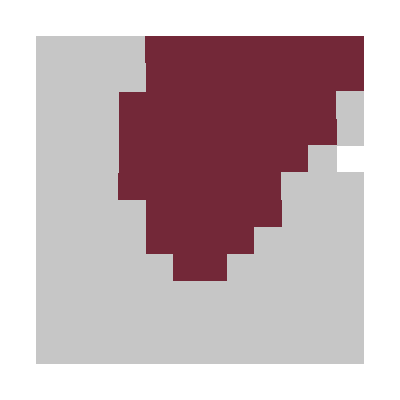

```mathematica
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-2}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-2,White,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
```

```mathematica
Export[NotebookDirectory[]<>"extSkeletonModel-patternTypes.pdf",
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-2}&/@Select[Flatten/@phaseDiagramMorphExtSkeletonModel,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-2,White,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
];
```

#### Pattern kymographs

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-extSkeletonModel.h5";
data=dataKymo[{filenameT
},{10^3./4,10^3/4}];
ListDensityPlot[Total@data[[{1,2},-400;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^3/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-extSkeletonModel.h5";
data=dataKymo[{filenameT
},{10^3./4,10^4/4}];
ListDensityPlot[Total@data[[{1,2},-400;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^3/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

### Denk et al.

```mathematica
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel.h5",
paramsDenkScaled,{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
0.5,
0.1,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->800]
```

{39.6223,25.}

{39.6223,39.6223}

{39.6223,62.7972}

{39.6223,99.5268}

{39.6223,157.739}

{39.6223,250.}

{39.6223,396.223}

{39.6223,627.972}

{39.6223,995.268}

{39.6223,1577.39}

{39.6223,2500.}

{39.6223,3962.23}

{62.7972,25.}

{62.7972,39.6223}

{62.7972,62.7972}

{62.7972,99.5268}

{62.7972,157.739}

{62.7972,250.}

{62.7972,396.223}

{62.7972,627.972}

{62.7972,995.268}

{62.7972,1577.39}

{62.7972,2500.}

{62.7972,3962.23}

{99.5268,25.}

{99.5268,39.6223}

{99.5268,62.7972}

{99.5268,99.5268}

{99.5268,157.739}

{99.5268,250.}

{99.5268,396.223}

{99.5268,627.972}

{99.5268,995.268}

{99.5268,1577.39}

{99.5268,2500.}

{99.5268,3962.23}

{157.739,25.}

{157.739,39.6223}

{157.739,62.7972}

{157.739,99.5268}

{157.739,157.739}

{157.739,250.}

{157.739,396.223}

{157.739,627.972}

{157.739,995.268}

{157.739,1577.39}

{157.739,2500.}

{157.739,3962.23}

{250.,25.}

{250.,39.6223}

{250.,62.7972}

{250.,99.5268}

{250.,157.739}

{250.,250.}

{250.,396.223}

{250.,627.972}

{250.,995.268}

{250.,1577.39}

{250.,2500.}

{250.,3962.23}

{396.223,25.}

{396.223,39.6223}

{396.223,62.7972}

{396.223,99.5268}

{396.223,157.739}

{396.223,250.}

{396.223,396.223}

{396.223,627.972}

{396.223,995.268}

{396.223,1577.39}

{396.223,2500.}

{396.223,3962.23}

{627.972,25.}

{627.972,39.6223}

{627.972,62.7972}

{627.972,99.5268}

{627.972,157.739}

{627.972,250.}

{627.972,396.223}

{627.972,627.972}

{627.972,995.268}

{627.972,1577.39}

{627.972,2500.}

{627.972,3962.23}

{995.268,25.}

{995.268,39.6223}

{995.268,62.7972}

{995.268,99.5268}

{995.268,157.739}

{995.268,250.}

{995.268,396.223}

{995.268,627.972}

{995.268,995.268}

{995.268,1577.39}

{995.268,2500.}

{995.268,3962.23}

{1577.39,25.}

{1577.39,39.6223}

{1577.39,62.7972}

{1577.39,99.5268}

{1577.39,157.739}

{1577.39,250.}

{1577.39,396.223}

{1577.39,627.972}

{1577.39,995.268}

{1577.39,1577.39}

{1577.39,2500.}

{1577.39,3962.23}

{2500.,25.}

{2500.,39.6223}

{2500.,62.7972}

{2500.,99.5268}

{2500.,157.739}

{2500.,250.}

{2500.,396.223}

{2500.,627.972}

{2500.,995.268}

{2500.,1577.39}

{2500.,2500.}

{2500.,3962.23}

{3962.23,25.}

{3962.23,39.6223}

{3962.23,62.7972}

{3962.23,99.5268}

{3962.23,157.739}

{3962.23,250.}

{3962.23,396.223}

{3962.23,627.972}

{3962.23,995.268}

{3962.23,1577.39}

{3962.23,2500.}

{3962.23,3962.23}

```mathematica
phaseDiagramMorphDenkModel=testSweepMultipleFilesMorph[{NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel.h5"
},"TimePoints"->2000];
```

-Graphics-

period: 18.8679, wavelength: 47.619

{1.99794,2.59794}

-Graphics-

period: 15.0376, wavelength: 47.619

{1.99794,2.79794}

-Graphics-

period: 40., wavelength: 45.4545

{2.19794,1.99794}

-Graphics-

period: 30.7692, wavelength: 45.4545

{2.19794,2.19794}

-Graphics-

period: 24.0964, wavelength: 43.4783

{2.19794,2.39794}

-Graphics-

period: 19.0476, wavelength: 43.4783

{2.19794,2.59794}

-Graphics-

period: 15.1515, wavelength: 45.4545

{2.19794,2.79794}

-Graphics-

period: 12.1212, wavelength: 50.

{2.19794,2.99794}

-Graphics-

period: 9.70874, wavelength: 47.619

{2.19794,3.19794}

-Graphics-

period: 7.84314, wavelength: 47.619

{2.19794,3.39794}

-Graphics-

period: 62.5, wavelength: 45.4545

{2.39794,1.79794}

-Graphics-

period: 44.4444, wavelength: 41.6667

{2.39794,1.99794}

-Graphics-

period: 32.7869, wavelength: 41.6667

{2.39794,2.19794}

-Graphics-

period: 25.3165, wavelength: 41.6667

{2.39794,2.39794}

-Graphics-

period: 19.6078, wavelength: 43.4783

{2.39794,2.59794}

-Graphics-

period: 15.625, wavelength: 41.6667

{2.39794,2.79794}

-Graphics-

period: 12.5, wavelength: 41.6667

{2.39794,2.99794}

-Graphics-

period: 10.101, wavelength: 43.4783

{2.39794,3.19794}

-Graphics-

period: 8., wavelength: 50.

{2.39794,3.39794}

-Graphics-

period: 52.6316, wavelength: 37.037

{2.59794,1.99794}

-Graphics-

period: 37.037, wavelength: 40.

{2.59794,2.19794}

-Graphics-

period: 27.7778, wavelength: 40.

{2.59794,2.39794}

-Graphics-

period: 21.0526, wavelength: 41.6667

{2.59794,2.59794}

-Graphics-

period: 16.5289, wavelength: 41.6667

{2.59794,2.79794}

-Graphics-

period: 13.3333, wavelength: 35.7143

{2.59794,2.99794}

-Graphics-

period: 10.8108, wavelength: 41.6667

{2.59794,3.19794}

-Graphics-

period: 8.69565, wavelength: 41.6667

{2.59794,3.39794}

-Graphics-

period: 7.01754, wavelength: 50.

{2.59794,3.59794}

-Graphics-

period: 68.9655, wavelength: 43.4783

{2.79794,1.99794}

-Graphics-

period: 45.4545, wavelength: 33.3333

{2.79794,2.19794}

-Graphics-

period: 32.2581, wavelength: 37.037

{2.79794,2.39794}

-Graphics-

period: 23.8095, wavelength: 35.7143

{2.79794,2.59794}

-Graphics-

period: 18.1818, wavelength: 37.037

{2.79794,2.79794}

-Graphics-

period: 14.3885, wavelength: 35.7143

{2.79794,2.99794}

-Graphics-

period: 11.6279, wavelength: 34.4828

{2.79794,3.19794}

-Graphics-

period: 50., wavelength: 40.

{2.79794,3.39794}

-Graphics-

period: 50., wavelength: 45.4545

{2.79794,3.59794}

-Graphics-

period: 62.5, wavelength: 45.4545

{2.99794,2.19794}

-Graphics-

period: 40.8163, wavelength: 37.037

{2.99794,2.39794}

-Graphics-

period: 28.5714, wavelength: 35.7143

{2.99794,2.59794}

-Graphics-

period: 20.8333, wavelength: 33.3333

{2.99794,2.79794}

-Graphics-

period: 50., wavelength: 32.2581

{2.99794,2.99794}

-Graphics-

period: 50., wavelength: 30.303

{2.99794,3.19794}

-Graphics-

period: 50., wavelength: 32.2581

{2.99794,3.39794}

-Graphics-

period: 50., wavelength: 41.6667

{2.99794,3.59794}

-Graphics-

period: 60.6061, wavelength: 47.619

{3.19794,2.39794}

-Graphics-

period: 37.7358, wavelength: 37.037

{3.19794,2.59794}

-Graphics-

period: 25.641, wavelength: 29.4118

{3.19794,2.79794}

-Graphics-

period: 51.2821, wavelength: 30.303

{3.19794,2.99794}

-Graphics-

period: 51.2821, wavelength: 28.5714

{3.19794,3.19794}

-Graphics-

period: 50., wavelength: 32.2581

{3.19794,3.39794}

-Graphics-

period: 48.7805, wavelength: 35.7143

{3.19794,3.59794}

-Graphics-

period: 35.0877, wavelength: 41.6667

{3.39794,2.79794}

-Graphics-

period: 50., wavelength: 28.5714

{3.39794,2.99794}

-Graphics-

period: 51.2821, wavelength: 28.5714

{3.39794,3.19794}

-Graphics-

period: 50., wavelength: 27.7778

{3.39794,3.39794}

-Graphics-

period: 51.2821, wavelength: 28.5714

{3.39794,3.59794}

-Graphics-

period: 48.7805, wavelength: 38.4615

{3.59794,2.99794}

-Graphics-

period: 50., wavelength: 29.4118

{3.59794,3.19794}

-Graphics-

period: 51.2821, wavelength: 24.3902

{3.59794,3.39794}

-Graphics-

period: 51.2821, wavelength: 27.027

{3.59794,3.59794}

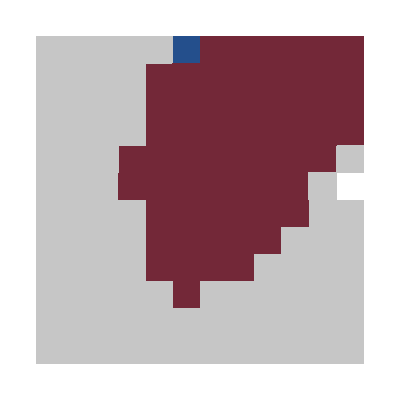

```mathematica
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-2}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-2,White,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
```

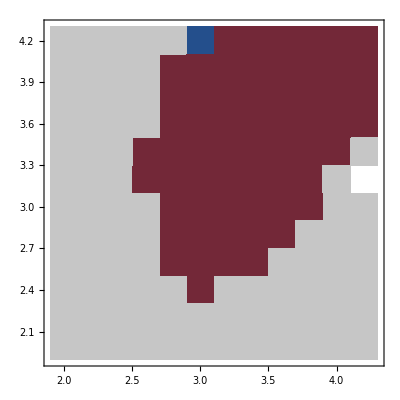

```mathematica
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-2}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-2,White,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All}
]
```

```mathematica
Export[NotebookDirectory[]<>"DenkModel-patternTypes.pdf",
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-2}&/@Select[Flatten/@phaseDiagramMorphDenkModel,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-2,White,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
];
```

Test the standing-wave simulation again in a finer kymograph:

```mathematica
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel-fine.h5",
paramsDenkScaled,{{rhoD,{10^3.}/4},{rhoE,{10^4.2}/4}},
0.2,
0.2,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2800,
"MaxSimulationTime"->800]
```

{250.,3962.23}

```mathematica
phaseDiagramMorphDenkModel=testSweepMultipleFilesMorph[{NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel-fine.h5"
},"TimePoints"->1000];
```

-Graphics-

period: 14.2857, wavelength: 22.7273

{2.39794,3.59794}

#### Pattern kymographs

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel-fine.h5";
data=dataKymo[{filenameT
},{10^3./4,10^4.2/4}];
ListDensityPlot[Total@data[[{1,2},-200;;]],ColorFunction->GrayLevel,InterpolationOrder->0,AspectRatio->3,PlotLegends->Automatic]
```

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel.h5";
data=dataKymo[{filenameT
},{10^3./4,10^3/4}];
ListDensityPlot[Total@data[[{1,2},-400;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^3/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel.h5";
data=dataKymo[{filenameT
},{10^3./4,10^4/4}];
ListDensityPlot[Total@data[[{1,2},-400;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^3/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-DenkModel.h5";
data=dataKymo[{filenameT
},{10^3.8/4,10^3./4}];
ListDensityPlot[Total@data[[{1,2},-400;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^3.8/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

## Phase diagram simulation sweeps

```mathematica
Do[
Print["parameters: ",ks];
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-kD_"<>toString[ks[[1]]]<>"-kdD_"<>toString[ks[[2]]]<>".h5",
Join[{kD->ks[[1]],kdD->(ks[[2]])},DeleteCases[params,(kD->_)|(kdD->_)]],{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
0.3,
0.3,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->2000],
{ks,Flatten[Outer[List,(kD/.params)*10^Range[-1,0.5,0.5],(kdD/.params)*10^Range[-0.5,1.5,0.5]],1]}]//AbsoluteTiming
```

```mathematica
Do[
Print["parameters: ",ks];
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-mu_"<>toString[ks[[1]]]<>"-kdD_"<>toString[ks[[2]]]<>".h5",
Join[{μ->ks[[1]],kdD->(ks[[2]])},DeleteCases[params,(μ->_)|(kdD->_)]],{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
0.3,
0.3,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->2000],
{ks,Flatten[Outer[List,{50,100},(kdD/.params)*10^Range[-0.5,1.5,0.5]],1]}]//AbsoluteTiming
```

```mathematica
Do[
Print["parameters: ",ks];
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-DdDde_"<>toString[ks[[1]]]<>"-kdD_"<>toString[ks[[2]]]<>".h5",
Join[{Dd->ks[[1]],Dde->ks[[1]],kdD->(ks[[2]])},DeleteCases[params,(Dd->_)|(Dde->_)|(kdD->_)]],{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
0.3,
0.3,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->2000],
{ks,Flatten[Outer[List,{0.01,0.1},(kdD/.params)*10^Range[-0.5,1.5,0.5]],1]}]//AbsoluteTiming
```

```mathematica
Do[
Print["parameters: ",ks];
simSweepTA[NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-kde_"<>toString[ks[[1]]]<>"-kdD_"<>toString[ks[[2]]]<>".h5",
Join[{kde->ks[[1]],kdD->(ks[[2]])},DeleteCases[params,(kde->_)|(kdD->_)]],{{rhoD,10^Range[2,4.3,0.2]/4},{rhoE,10^Range[2,4.3,0.2]/4}},
2,
0.1,
"BC"->"Reflective",
"GridPoints"->250,
"FinerGridIfFailed"->500,
"TIni"->2000,
"MaxSimulationTime"->2000],
{ks,Flatten[Outer[List,{0.1,2},(kdD/.params)*10^Range[-0.5,1.5,0.5]],1]}]//AbsoluteTiming
```

## Analysis of phase diagram sweeps

## Morphological pattern classification

### kD-kdD sweep

```mathematica
analysisListMorph=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-kD_"<>toString[kD]<>"-kdD_"<>toString[kdD]<>".h5"
},
testSweepMultipleFilesMorph[{filename
},"TimePoints"->Floor[1000/0.3]]
],{kD,(kD/.params)*10^Range[-1,0.5,0.5]},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

-Graphics-

period: 303., wavelength: 66.8

{2.19794,1.99794}

-Graphics-

period: 238.071, wavelength: 66.8

{2.19794,2.19794}

-Graphics-

period: 175.421, wavelength: 66.8

{2.19794,2.39794}

-Graphics-

period: 138.875, wavelength: 66.8

{2.19794,2.59794}

-Graphics-

period: 107.516, wavelength: 66.8

{2.19794,2.79794}

-Graphics-

period: 666.6, wavelength: 83.5

{2.39794,1.59794}

-Graphics-

period: 416.625, wavelength: 66.8

{2.39794,1.79794}

-Graphics-

period: 303., wavelength: 66.8

{2.39794,1.99794}

-Graphics-

period: 238.071, wavelength: 55.6667

{2.39794,2.19794}

-Graphics-

period: 175.421, wavelength: 55.6667

{2.39794,2.39794}

-Graphics-

period: 138.875, wavelength: 55.6667

{2.39794,2.59794}

-Graphics-

period: 107.516, wavelength: 47.7143

{2.39794,2.79794}

-Graphics-

period: 83.325, wavelength: 55.6667

{2.39794,2.99794}

-Graphics-

period: 65.3529, wavelength: 55.6667

{2.39794,3.19794}

-Graphics-

period: 1111., wavelength: 83.5

{2.59794,1.39794}

-Graphics-

period: 666.6, wavelength: 83.5

{2.59794,1.59794}

-Graphics-

period: 476.143, wavelength: 66.8

{2.59794,1.79794}

-Graphics-

period: 333.3, wavelength: 55.6667

{2.59794,1.99794}

-Graphics-

period: 256.385, wavelength: 55.6667

{2.59794,2.19794}

-Graphics-

period: 196.059, wavelength: 55.6667

{2.59794,2.39794}

-Graphics-

period: 70.9149, wavelength: 47.7143

{2.59794,3.19794}

-Graphics-

period: 53.7581, wavelength: 47.7143

{2.59794,3.39794}

-Graphics-

period: 41.6625, wavelength: 47.7143

{2.59794,3.59794}

-Graphics-

period: 1666.5, wavelength: 83.5

{2.79794,1.39794}

-Graphics-

period: 833.25, wavelength: 66.8

{2.79794,1.59794}

-Graphics-

period: 555.5, wavelength: 55.6667

{2.79794,1.79794}

-Graphics-

period: 416.625, wavelength: 55.6667

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 55.6667

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 55.6667

{2.79794,2.39794}

-Graphics-

period: 48.3043, wavelength: 37.1111

{2.79794,3.59794}

-Graphics-

period: 1666.5, wavelength: 66.8

{2.99794,1.59794}

-Graphics-

period: 833.25, wavelength: 66.8

{2.99794,1.79794}

-Graphics-

period: 555.5, wavelength: 55.6667

{2.99794,1.99794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.99794,2.19794}

-Graphics-

period: 277.75, wavelength: 41.75

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 47.7143

{2.99794,2.59794}

-Graphics-

period: 151.5, wavelength: 47.7143

{2.99794,2.79794}

-Graphics-

period: 833.25, wavelength: 66.8

{3.19794,1.99794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.19794,2.19794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 238.071, wavelength: 47.7143

{3.19794,2.59794}

-Graphics-

period: 175.421, wavelength: 41.75

{3.19794,2.79794}

-Graphics-

period: 133.32, wavelength: 47.7143

{3.19794,2.99794}

-Graphics-

period: 101., wavelength: 47.7143

{3.19794,3.19794}

-Graphics-

period: 1111., wavelength: 55.6667

{3.39794,2.19794}

-Graphics-

period: 476.143, wavelength: 55.6667

{3.39794,2.39794}

-Graphics-

period: 303., wavelength: 47.7143

{3.39794,2.59794}

-Graphics-

period: 222.2, wavelength: 41.75

{3.39794,2.79794}

-Graphics-

period: 158.714, wavelength: 37.1111

{3.39794,2.99794}

-Graphics-

period: 119.036, wavelength: 37.1111

{3.39794,3.19794}

-Graphics-

period: 92.5833, wavelength: 41.75

{3.39794,3.39794}

-Graphics-

period: 72.4565, wavelength: 41.75

{3.39794,3.59794}

-Graphics-

period: 1111., wavelength: 66.8

{3.59794,2.39794}

-Graphics-

period: 476.143, wavelength: 55.6667

{3.59794,2.59794}

-Graphics-

period: 303., wavelength: 47.7143

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 41.75

{3.59794,2.99794}

-Graphics-

period: 138.875, wavelength: 37.1111

{3.59794,3.19794}

-Graphics-

period: 104.156, wavelength: 33.4

{3.59794,3.39794}

-Graphics-

period: 81.2927, wavelength: 37.1111

{3.59794,3.59794}

-Graphics-

period: 256.385, wavelength: 55.6667

{1.99794,2.19794}

-Graphics-

period: 196.059, wavelength: 55.6667

{1.99794,2.39794}

-Graphics-

period: 151.5, wavelength: 55.6667

{1.99794,2.59794}

-Graphics-

period: 114.931, wavelength: 55.6667

{1.99794,2.79794}

-Graphics-

period: 90.0811, wavelength: 55.6667

{1.99794,2.99794}

-Graphics-

period: 72.4565, wavelength: 55.6667

{1.99794,3.19794}

-Graphics-

period: 476.143, wavelength: 55.6667

{2.19794,1.79794}

-Graphics-

period: 333.3, wavelength: 55.6667

{2.19794,1.99794}

-Graphics-

period: 256.385, wavelength: 55.6667

{2.19794,2.19794}

-Graphics-

period: 196.059, wavelength: 47.7143

{2.19794,2.39794}

-Graphics-

period: 151.5, wavelength: 47.7143

{2.19794,2.59794}

-Graphics-

period: 114.931, wavelength: 47.7143

{2.19794,2.79794}

-Graphics-

period: 92.5833, wavelength: 47.7143

{2.19794,2.99794}

-Graphics-

period: 72.4565, wavelength: 47.7143

{2.19794,3.19794}

-Graphics-

period: 56.4915, wavelength: 41.75

{2.19794,3.39794}

-Graphics-

period: 44.44, wavelength: 41.75

{2.19794,3.59794}

-Graphics-

period: 666.6, wavelength: 55.6667

{2.39794,1.59794}

-Graphics-

period: 476.143, wavelength: 55.6667

{2.39794,1.79794}

-Graphics-

period: 333.3, wavelength: 47.7143

{2.39794,1.99794}

-Graphics-

period: 256.385, wavelength: 47.7143

{2.39794,2.19794}

-Graphics-

period: 196.059, wavelength: 47.7143

{2.39794,2.39794}

-Graphics-

period: 158.714, wavelength: 47.7143

{2.39794,2.59794}

-Graphics-

period: 123.444, wavelength: 41.75

{2.39794,2.79794}

-Graphics-

period: 98.0294, wavelength: 47.7143

{2.39794,2.99794}

-Graphics-

period: 833.25, wavelength: 55.6667

{2.59794,1.59794}

-Graphics-

period: 555.5, wavelength: 55.6667

{2.59794,1.79794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.59794,1.99794}

-Graphics-

period: 277.75, wavelength: 47.7143

{2.59794,2.19794}

-Graphics-

period: 222.2, wavelength: 41.75

{2.59794,2.39794}

-Graphics-

period: 166.65, wavelength: 41.75

{2.59794,2.59794}

-Graphics-

period: 133.32, wavelength: 33.4

{2.59794,2.79794}

-Graphics-

period: 107.516, wavelength: 47.7143

{2.59794,2.99794}

-Graphics-

period: 83.325, wavelength: 47.7143

{2.59794,3.19794}

-Graphics-

period: 1666.5, wavelength: 66.8

{2.79794,1.59794}

-Graphics-

period: 666.6, wavelength: 55.6667

{2.79794,1.79794}

-Graphics-

period: 476.143, wavelength: 55.6667

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 238.071, wavelength: 41.75

{2.79794,2.39794}

-Graphics-

period: 185.167, wavelength: 41.75

{2.79794,2.59794}

-Graphics-

period: 144.913, wavelength: 37.1111

{2.79794,2.79794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.79794,2.99794}

-Graphics-

period: 92.5833, wavelength: 37.1111

{2.79794,3.19794}

-Graphics-

period: 74.0667, wavelength: 47.7143

{2.79794,3.39794}

-Graphics-

period: 59.5179, wavelength: 23.8571

{2.79794,3.59794}

-Graphics-

period: 666.6, wavelength: 47.7143

{2.99794,1.99794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.99794,2.19794}

-Graphics-

period: 277.75, wavelength: 41.75

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 37.1111

{2.99794,2.59794}

-Graphics-

period: 151.5, wavelength: 37.1111

{2.99794,2.79794}

-Graphics-

period: 123.444, wavelength: 33.4

{2.99794,2.99794}

-Graphics-

period: 98.0294, wavelength: 30.3636

{2.99794,3.19794}

-Graphics-

period: 79.3571, wavelength: 33.4

{2.99794,3.39794}

-Graphics-

period: 65.3529, wavelength: 33.4

{2.99794,3.59794}

-Graphics-

period: 555.5, wavelength: 47.7143

{3.19794,2.19794}

-Graphics-

period: 370.333, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 238.071, wavelength: 41.75

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 128.192, wavelength: 33.4

{3.19794,2.99794}

-Graphics-

period: 101., wavelength: 33.4

{3.19794,3.19794}

-Graphics-

period: 83.325, wavelength: 27.8333

{3.19794,3.39794}

-Graphics-

period: 68.0204, wavelength: 30.3636

{3.19794,3.59794}

-Graphics-

period: 833.25, wavelength: 20.875

{3.39794,2.39794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.39794,2.59794}

-Graphics-

period: 208.313, wavelength: 37.1111

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 33.4

{3.39794,2.99794}

-Graphics-

period: 107.516, wavelength: 30.3636

{3.39794,3.19794}

-Graphics-

period: 85.4615, wavelength: 27.8333

{3.39794,3.39794}

-Graphics-

period: 70.9149, wavelength: 27.8333

{3.39794,3.59794}

-Graphics-

period: 303., wavelength: 47.7143

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 47.7143

{3.59794,2.99794}

-Graphics-

period: 123.444, wavelength: 37.1111

{3.59794,3.19794}

-Graphics-

period: 92.5833, wavelength: 30.3636

{3.59794,3.39794}

-Graphics-

period: 72.4565, wavelength: 23.8571

{3.59794,3.59794}

-Graphics-

period: 166.65, wavelength: 47.7143

{1.79794,2.59794}

-Graphics-

period: 128.192, wavelength: 41.75

{1.79794,2.79794}

-Graphics-

period: 101., wavelength: 41.75

{1.79794,2.99794}

-Graphics-

period: 77.5116, wavelength: 47.7143

{1.79794,3.19794}

-Graphics-

period: 61.7222, wavelength: 41.75

{1.79794,3.39794}

-Graphics-

period: 49.7463, wavelength: 41.75

{1.79794,3.59794}

-Graphics-

period: 277.75, wavelength: 47.7143

{1.99794,2.19794}

-Graphics-

period: 208.313, wavelength: 41.75

{1.99794,2.39794}

-Graphics-

period: 158.714, wavelength: 41.75

{1.99794,2.59794}

-Graphics-

period: 123.444, wavelength: 37.1111

{1.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 37.1111

{1.99794,2.99794}

-Graphics-

period: 77.5116, wavelength: 37.1111

{1.99794,3.19794}

-Graphics-

period: 61.7222, wavelength: 37.1111

{1.99794,3.39794}

-Graphics-

period: 49.7463, wavelength: 41.75

{1.99794,3.59794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.19794,1.99794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.19794,2.19794}

-Graphics-

period: 208.313, wavelength: 41.75

{2.19794,2.39794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.19794,2.59794}

-Graphics-

period: 123.444, wavelength: 33.4

{2.19794,2.79794}

-Graphics-

period: 101., wavelength: 30.3636

{2.19794,2.99794}

-Graphics-

period: 81.2927, wavelength: 37.1111

{2.19794,3.19794}

-Graphics-

period: 65.3529, wavelength: 37.1111

{2.19794,3.39794}

-Graphics-

period: 52.0781, wavelength: 37.1111

{2.19794,3.59794}

-Graphics-

period: 555.5, wavelength: 47.7143

{2.39794,1.79794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.39794,1.99794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.39794,2.19794}

-Graphics-

period: 208.313, wavelength: 41.75

{2.39794,2.39794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.39794,2.59794}

-Graphics-

period: 128.192, wavelength: 33.4

{2.39794,2.79794}

-Graphics-

period: 104.156, wavelength: 33.4

{2.39794,2.99794}

-Graphics-

period: 83.325, wavelength: 33.4

{2.39794,3.19794}

-Graphics-

period: 68.0204, wavelength: 33.4

{2.39794,3.39794}

-Graphics-

period: 56.4915, wavelength: 33.4

{2.39794,3.59794}

-Graphics-

period: 666.6, wavelength: 41.75

{2.59794,1.79794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.59794,1.99794}

-Graphics-

period: 277.75, wavelength: 41.75

{2.59794,2.19794}

-Graphics-

period: 208.313, wavelength: 37.1111

{2.59794,2.39794}

-Graphics-

period: 166.65, wavelength: 33.4

{2.59794,2.59794}

-Graphics-

period: 128.192, wavelength: 30.3636

{2.59794,2.79794}

-Graphics-

period: 104.156, wavelength: 30.3636

{2.59794,2.99794}

-Graphics-

period: 85.4615, wavelength: 30.3636

{2.59794,3.19794}

-Graphics-

period: 70.9149, wavelength: 30.3636

{2.59794,3.39794}

-Graphics-

period: 58.4737, wavelength: 30.3636

{2.59794,3.59794}

-Graphics-

period: 476.143, wavelength: 41.75

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 41.75

{2.79794,2.39794}

-Graphics-

period: 166.65, wavelength: 37.1111

{2.79794,2.59794}

-Graphics-

period: 133.32, wavelength: 30.3636

{2.79794,2.79794}

-Graphics-

period: 107.516, wavelength: 30.3636

{2.79794,2.99794}

-Graphics-

period: 87.7105, wavelength: 30.3636

{2.79794,3.19794}

-Graphics-

period: 72.4565, wavelength: 27.8333

{2.79794,3.39794}

-Graphics-

period: 60.6, wavelength: 27.8333

{2.79794,3.59794}

-Graphics-

period: 416.625, wavelength: 47.7143

{2.99794,2.19794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 41.75

{2.99794,2.59794}

-Graphics-

period: 138.875, wavelength: 33.4

{2.99794,2.79794}

-Graphics-

period: 107.516, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 87.7105, wavelength: 23.8571

{2.99794,3.19794}

-Graphics-

period: 72.4565, wavelength: 27.8333

{2.99794,3.39794}

-Graphics-

period: 60.6, wavelength: 27.8333

{2.99794,3.59794}

-Graphics-

period: 416.625, wavelength: 41.75

{3.19794,2.39794}

-Graphics-

period: 222.2, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 41.75

{3.19794,2.79794}

-Graphics-

period: 119.036, wavelength: 33.4

{3.19794,2.99794}

-Graphics-

period: 90.0811, wavelength: 25.6923

{3.19794,3.19794}

-Graphics-

period: 72.4565, wavelength: 25.6923

{3.19794,3.39794}

-Graphics-

period: 60.6, wavelength: 23.8571

{3.19794,3.59794}

-Graphics-

period: 196.059, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 41.75

{3.39794,2.99794}

-Graphics-

period: 101., wavelength: 33.4

{3.39794,3.19794}

-Graphics-

period: 75.75, wavelength: 23.8571

{3.39794,3.39794}

-Graphics-

period: 59.5179, wavelength: 25.6923

{3.39794,3.59794}

-Graphics-

period: 175.421, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 119.036, wavelength: 33.4

{3.59794,3.19794}

-Graphics-

period: 90.0811, wavelength: 33.4

{3.59794,3.39794}

-Graphics-

period: 64.0962, wavelength: 30.3636

{3.59794,3.59794}

-Graphics-

period: 85.4615, wavelength: 33.4

{1.59794,3.19794}

-Graphics-

period: 68.0204, wavelength: 33.4

{1.59794,3.39794}

-Graphics-

period: 53.7581, wavelength: 33.4

{1.59794,3.59794}

-Graphics-

period: 128.192, wavelength: 33.4

{1.79794,2.79794}

-Graphics-

period: 104.156, wavelength: 33.4

{1.79794,2.99794}

-Graphics-

period: 81.2927, wavelength: 33.4

{1.79794,3.19794}

-Graphics-

period: 65.3529, wavelength: 27.8333

{1.79794,3.39794}

-Graphics-

period: 52.9048, wavelength: 33.4

{1.79794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{1.99794,2.39794}

-Graphics-

period: 158.714, wavelength: 33.4

{1.99794,2.59794}

-Graphics-

period: 123.444, wavelength: 33.4

{1.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{1.99794,2.99794}

-Graphics-

period: 79.3571, wavelength: 33.4

{1.99794,3.19794}

-Graphics-

period: 65.3529, wavelength: 27.8333

{1.99794,3.39794}

-Graphics-

period: 52.9048, wavelength: 30.3636

{1.99794,3.59794}

-Graphics-

period: 256.385, wavelength: 30.3636

{2.19794,2.19794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.19794,2.39794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.19794,2.59794}

-Graphics-

period: 119.036, wavelength: 27.8333

{2.19794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{2.19794,2.99794}

-Graphics-

period: 79.3571, wavelength: 27.8333

{2.19794,3.19794}

-Graphics-

period: 65.3529, wavelength: 23.8571

{2.19794,3.39794}

-Graphics-

period: 53.7581, wavelength: 27.8333

{2.19794,3.59794}

-Graphics-

period: 256.385, wavelength: 33.4

{2.39794,2.19794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.39794,2.39794}

-Graphics-

period: 151.5, wavelength: 25.6923

{2.39794,2.59794}

-Graphics-

period: 119.036, wavelength: 25.6923

{2.39794,2.79794}

-Graphics-

period: 95.2286, wavelength: 27.8333

{2.39794,2.99794}

-Graphics-

period: 77.5116, wavelength: 25.6923

{2.39794,3.19794}

-Graphics-

period: 65.3529, wavelength: 25.6923

{2.39794,3.39794}

-Graphics-

period: 54.6393, wavelength: 25.6923

{2.39794,3.59794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.59794,2.19794}

-Graphics-

period: 196.059, wavelength: 37.1111

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.59794,2.59794}

-Graphics-

period: 119.036, wavelength: 30.3636

{2.59794,2.79794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{2.59794,2.99794}

-Graphics-

period: 77.5116, wavelength: 27.8333

{2.59794,3.19794}

-Graphics-

period: 64.0962, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 53.7581, wavelength: 22.2667

{2.59794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 123.444, wavelength: 30.3636

{2.79794,2.79794}

-Graphics-

period: 95.2286, wavelength: 22.2667

{2.79794,2.99794}

-Graphics-

period: 75.75, wavelength: 23.8571

{2.79794,3.19794}

-Graphics-

period: 62.8868, wavelength: 23.8571

{2.79794,3.39794}

-Graphics-

period: 52.9048, wavelength: 20.875

{2.79794,3.59794}

-Graphics-

period: 175.421, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 77.5116, wavelength: 27.8333

{2.99794,3.19794}

-Graphics-

period: 61.7222, wavelength: 25.6923

{2.99794,3.39794}

-Graphics-

period: 52.0781, wavelength: 19.6471

{2.99794,3.59794}

-Graphics-

period: 144.913, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 104.156, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 81.2927, wavelength: 27.8333

{3.19794,3.19794}

-Graphics-

period: 64.0962, wavelength: 25.6923

{3.19794,3.39794}

-Graphics-

period: 51.2769, wavelength: 23.8571

{3.19794,3.59794}

-Graphics-

period: 123.444, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 85.4615, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 68.0204, wavelength: 27.8333

{3.39794,3.39794}

-Graphics-

period: 53.7581, wavelength: 27.8333

{3.39794,3.59794}

-Graphics-

period: 107.516, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 70.9149, wavelength: 23.8571

{3.59794,3.39794}

-Graphics-

period: 56.4915, wavelength: 25.6923

{3.59794,3.59794}

-Graphics-

period: 66.66, wavelength: 25.6923

{1.59794,3.39794}

-Graphics-

period: 53.7581, wavelength: 27.8333

{1.59794,3.59794}

-Graphics-

period: 98.0294, wavelength: 25.6923

{1.79794,2.99794}

-Graphics-

period: 79.3571, wavelength: 23.8571

{1.79794,3.19794}

-Graphics-

period: 64.0962, wavelength: 22.2667

{1.79794,3.39794}

-Graphics-

period: 52.0781, wavelength: 23.8571

{1.79794,3.59794}

-Graphics-

period: 119.036, wavelength: 25.6923

{1.99794,2.79794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{1.99794,2.99794}

-Graphics-

period: 74.0667, wavelength: 23.8571

{1.99794,3.19794}

-Graphics-

period: 60.6, wavelength: 20.875

{1.99794,3.39794}

-Graphics-

period: 50.5, wavelength: 23.8571

{1.99794,3.59794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.19794,2.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{2.19794,2.79794}

-Graphics-

period: 87.7105, wavelength: 22.2667

{2.19794,2.99794}

-Graphics-

period: 70.9149, wavelength: 22.2667

{2.19794,3.19794}

-Graphics-

period: 58.4737, wavelength: 18.5556

{2.19794,3.39794}

-Graphics-

period: 49.0147, wavelength: 19.6471

{2.19794,3.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.39794,2.59794}

-Graphics-

period: 104.156, wavelength: 25.6923

{2.39794,2.79794}

-Graphics-

period: 83.325, wavelength: 23.8571

{2.39794,2.99794}

-Graphics-

period: 68.0204, wavelength: 20.875

{2.39794,3.19794}

-Graphics-

period: 56.4915, wavelength: 18.5556

{2.39794,3.39794}

-Graphics-

period: 47.6143, wavelength: 17.5789

{2.39794,3.59794}

-Graphics-

period: 138.875, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 104.156, wavelength: 23.8571

{2.59794,2.79794}

-Graphics-

period: 83.325, wavelength: 22.2667

{2.59794,2.99794}

-Graphics-

period: 66.66, wavelength: 20.875

{2.59794,3.19794}

-Graphics-

period: 54.6393, wavelength: 20.875

{2.59794,3.39794}

-Graphics-

period: 45.6575, wavelength: 18.5556

{2.59794,3.59794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 107.516, wavelength: 25.6923

{2.79794,2.79794}

-Graphics-

period: 81.2927, wavelength: 22.2667

{2.79794,2.99794}

-Graphics-

period: 65.3529, wavelength: 23.8571

{2.79794,3.19794}

-Graphics-

period: 53.7581, wavelength: 22.2667

{2.79794,3.39794}

-Graphics-

period: 44.44, wavelength: 18.5556

{2.79794,3.59794}

-Graphics-

period: 119.036, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 83.325, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 65.3529, wavelength: 20.875

{2.99794,3.19794}

-Graphics-

period: 54.6393, wavelength: 23.8571

{2.99794,3.39794}

-Graphics-

period: 43.8553, wavelength: 19.6471

{2.99794,3.59794}

-Graphics-

period: 95.2286, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 68.0204, wavelength: 19.6471

{3.19794,3.19794}

-Graphics-

period: 53.7581, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 45.0405, wavelength: 23.8571

{3.19794,3.59794}

-Graphics-

period: 81.2927, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 56.4915, wavelength: 19.6471

{3.39794,3.39794}

-Graphics-

period: 45.0405, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 68.0204, wavelength: 19.6471

{3.59794,3.39794}

-Graphics-

period: 46.2917, wavelength: 16.7

{3.59794,3.59794}

-Graphics-

period: 81.2927, wavelength: 47.7143

{2.39794,2.99794}

-Graphics-

period: 64.0962, wavelength: 41.75

{2.59794,3.19794}

-Graphics-

period: 50.5, wavelength: 41.75

{2.59794,3.39794}

-Graphics-

period: 1111., wavelength: 66.8

{2.79794,1.59794}

-Graphics-

period: 666.6, wavelength: 66.8

{2.79794,1.79794}

-Graphics-

period: 416.625, wavelength: 55.6667

{2.79794,1.99794}

-Graphics-

period: 41.1481, wavelength: 37.1111

{2.79794,3.59794}

-Graphics-

period: 833.25, wavelength: 66.8

{2.99794,1.79794}

-Graphics-

period: 555.5, wavelength: 55.6667

{2.99794,1.99794}

-Graphics-

period: 370.333, wavelength: 55.6667

{2.99794,2.19794}

-Graphics-

period: 833.25, wavelength: 66.8

{3.19794,1.99794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.19794,2.19794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 1111., wavelength: 66.8

{3.39794,2.19794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.39794,2.39794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.39794,2.59794}

-Graphics-

period: 222.2, wavelength: 41.75

{3.39794,2.79794}

-Graphics-

period: 151.5, wavelength: 41.75

{3.39794,2.99794}

-Graphics-

period: 107.516, wavelength: 37.1111

{3.39794,3.19794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.59794,2.59794}

-Graphics-

period: 303., wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 138.875, wavelength: 37.1111

{3.59794,3.19794}

-Graphics-

period: 101., wavelength: 37.1111

{3.59794,3.39794}

-Graphics-

period: 75.75, wavelength: 37.1111

{3.59794,3.59794}

-Graphics-

period: 175.421, wavelength: 47.7143

{2.19794,2.39794}

-Graphics-

period: 138.875, wavelength: 47.7143

{2.19794,2.59794}

-Graphics-

period: 66.66, wavelength: 41.75

{2.19794,3.19794}

-Graphics-

period: 52.9048, wavelength: 41.75

{2.19794,3.39794}

-Graphics-

period: 476.143, wavelength: 55.6667

{2.39794,1.79794}

-Graphics-

period: 333.3, wavelength: 47.7143

{2.39794,1.99794}

-Graphics-

period: 238.071, wavelength: 47.7143

{2.39794,2.19794}

-Graphics-

period: 185.167, wavelength: 47.7143

{2.39794,2.39794}

-Graphics-

period: 144.913, wavelength: 41.75

{2.39794,2.59794}

-Graphics-

period: 42.1899, wavelength: 37.1111

{2.39794,3.59794}

-Graphics-

period: 1111., wavelength: 55.6667

{2.59794,1.59794}

-Graphics-

period: 555.5, wavelength: 55.6667

{2.59794,1.79794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.59794,1.99794}

-Graphics-

period: 277.75, wavelength: 47.7143

{2.59794,2.19794}

-Graphics-

period: 208.313, wavelength: 41.75

{2.59794,2.39794}

-Graphics-

period: 158.714, wavelength: 41.75

{2.59794,2.59794}

-Graphics-

period: 666.6, wavelength: 55.6667

{2.79794,1.79794}

-Graphics-

period: 416.625, wavelength: 47.7143

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 37.1111

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 41.75

{2.79794,2.39794}

-Graphics-

period: 175.421, wavelength: 37.1111

{2.79794,2.59794}

-Graphics-

period: 133.32, wavelength: 41.75

{2.79794,2.79794}

-Graphics-

period: 666.6, wavelength: 55.6667

{2.99794,1.99794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.99794,2.19794}

-Graphics-

period: 256.385, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.99794,2.79794}

-Graphics-

period: 114.931, wavelength: 30.3636

{2.99794,2.99794}

-Graphics-

period: 90.0811, wavelength: 37.1111

{2.99794,3.19794}

-Graphics-

period: 70.9149, wavelength: 30.3636

{2.99794,3.39794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.19794,2.19794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 238.071, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 128.192, wavelength: 33.4

{3.19794,2.99794}

-Graphics-

period: 98.0294, wavelength: 30.3636

{3.19794,3.19794}

-Graphics-

period: 79.3571, wavelength: 25.6923

{3.19794,3.39794}

-Graphics-

period: 64.0962, wavelength: 30.3636

{3.19794,3.59794}

-Graphics-

period: 833.25, wavelength: 47.7143

inverted SW

{3.39794,2.39794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.39794,2.59794}

-Graphics-

period: 208.313, wavelength: 41.75

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 33.4

{3.39794,2.99794}

-Graphics-

period: 107.516, wavelength: 27.8333

{3.39794,3.19794}

-Graphics-

period: 85.4615, wavelength: 27.8333

{3.39794,3.39794}

-Graphics-

period: 68.0204, wavelength: 22.2667

{3.39794,3.59794}

-Graphics-

period: 333.3, wavelength: 47.7143

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 41.75

{3.59794,2.99794}

-Graphics-

period: 123.444, wavelength: 30.3636

{3.59794,3.19794}

-Graphics-

period: 90.0811, wavelength: 23.8571

{3.59794,3.39794}

-Graphics-

period: 72.4565, wavelength: 23.8571

{3.59794,3.59794}

-Graphics-

period: 196.059, wavelength: 47.7143

{1.99794,2.39794}

-Graphics-

period: 151.5, wavelength: 41.75

{1.99794,2.59794}

-Graphics-

period: 114.931, wavelength: 37.1111

{1.99794,2.79794}

-Graphics-

period: 90.0811, wavelength: 41.75

{1.99794,2.99794}

-Graphics-

period: 70.9149, wavelength: 37.1111

{1.99794,3.19794}

-Graphics-

period: 56.4915, wavelength: 37.1111

{1.99794,3.39794}

-Graphics-

period: 44.44, wavelength: 33.4

{1.99794,3.59794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.19794,1.99794}

-Graphics-

period: 256.385, wavelength: 47.7143

{2.19794,2.19794}

-Graphics-

period: 196.059, wavelength: 41.75

{2.19794,2.39794}

-Graphics-

period: 144.913, wavelength: 37.1111

{2.19794,2.59794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.19794,2.79794}

-Graphics-

period: 92.5833, wavelength: 33.4

{2.19794,2.99794}

-Graphics-

period: 72.4565, wavelength: 37.1111

{2.19794,3.19794}

-Graphics-

period: 555.5, wavelength: 47.7143

{2.39794,1.79794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.39794,1.99794}

-Graphics-

period: 256.385, wavelength: 37.1111

{2.39794,2.19794}

-Graphics-

period: 196.059, wavelength: 37.1111

{2.39794,2.39794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.39794,2.59794}

-Graphics-

period: 119.036, wavelength: 33.4

{2.39794,2.79794}

-Graphics-

period: 95.2286, wavelength: 33.4

{2.39794,2.99794}

-Graphics-

period: 77.5116, wavelength: 30.3636

{2.39794,3.19794}

-Graphics-

period: 61.7222, wavelength: 33.4

{2.39794,3.39794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.59794,1.99794}

-Graphics-

period: 277.75, wavelength: 41.75

{2.59794,2.19794}

-Graphics-

period: 208.313, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 158.714, wavelength: 30.3636

{2.59794,2.59794}

-Graphics-

period: 123.444, wavelength: 30.3636

{2.59794,2.79794}

-Graphics-

period: 101., wavelength: 27.8333

{2.59794,2.99794}

-Graphics-

period: 81.2927, wavelength: 27.8333

{2.59794,3.19794}

-Graphics-

period: 65.3529, wavelength: 30.3636

{2.59794,3.39794}

-Graphics-

period: 52.9048, wavelength: 27.8333

{2.59794,3.59794}

-Graphics-

period: 476.143, wavelength: 41.75

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 37.1111

{2.79794,2.39794}

-Graphics-

period: 166.65, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 128.192, wavelength: 33.4

{2.79794,2.79794}

-Graphics-

period: 104.156, wavelength: 27.8333

{2.79794,2.99794}

-Graphics-

period: 83.325, wavelength: 25.6923

{2.79794,3.19794}

-Graphics-

period: 69.4375, wavelength: 25.6923

{2.79794,3.39794}

-Graphics-

period: 56.4915, wavelength: 23.8571

{2.79794,3.59794}

-Graphics-

period: 416.625, wavelength: 41.75

{2.99794,2.19794}

-Graphics-

period: 256.385, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 107.516, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 85.4615, wavelength: 23.8571

{2.99794,3.19794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{2.99794,3.39794}

-Graphics-

period: 58.4737, wavelength: 23.8571

{2.99794,3.59794}

-Graphics-

period: 476.143, wavelength: 33.4

inverted SW

{3.19794,2.39794}

-Graphics-

period: 222.2, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 41.75

{3.19794,2.79794}

-Graphics-

period: 114.931, wavelength: 27.8333

{3.19794,2.99794}

-Graphics-

period: 87.7105, wavelength: 27.8333

{3.19794,3.19794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{3.19794,3.39794}

-Graphics-

period: 59.5179, wavelength: 19.6471

{3.19794,3.59794}

-Graphics-

period: 196.059, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 138.875, wavelength: 37.1111

{3.39794,2.99794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{3.39794,3.19794}

-Graphics-

period: 72.4565, wavelength: 25.6923

{3.39794,3.39794}

-Graphics-

period: 59.5179, wavelength: 23.8571

{3.39794,3.59794}

-Graphics-

period: 175.421, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 123.444, wavelength: 37.1111

{3.59794,3.19794}

-Graphics-

period: 83.325, wavelength: 27.8333

{3.59794,3.39794}

-Graphics-

period: 61.7222, wavelength: 23.8571

{3.59794,3.59794}

-Graphics-

period: 123.444, wavelength: 33.4

{1.79794,2.79794}

-Graphics-

period: 98.0294, wavelength: 33.4

{1.79794,2.99794}

-Graphics-

period: 75.75, wavelength: 30.3636

{1.79794,3.19794}

-Graphics-

period: 60.6, wavelength: 30.3636

{1.79794,3.39794}

-Graphics-

period: 48.3043, wavelength: 30.3636

{1.79794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{1.99794,2.39794}

-Graphics-

period: 151.5, wavelength: 33.4

{1.99794,2.59794}

-Graphics-

period: 119.036, wavelength: 33.4

{1.99794,2.79794}

-Graphics-

period: 92.5833, wavelength: 30.3636

{1.99794,2.99794}

-Graphics-

period: 74.0667, wavelength: 27.8333

{1.99794,3.19794}

-Graphics-

period: 60.6, wavelength: 25.6923

{1.99794,3.39794}

-Graphics-

period: 48.3043, wavelength: 30.3636

{1.99794,3.59794}

-Graphics-

period: 256.385, wavelength: 33.4

{2.19794,2.19794}

-Graphics-

period: 196.059, wavelength: 30.3636

{2.19794,2.39794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.19794,2.59794}

-Graphics-

period: 114.931, wavelength: 27.8333

{2.19794,2.79794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{2.19794,2.99794}

-Graphics-

period: 75.75, wavelength: 25.6923

{2.19794,3.19794}

-Graphics-

period: 60.6, wavelength: 25.6923

{2.19794,3.39794}

-Graphics-

period: 49.7463, wavelength: 27.8333

{2.19794,3.59794}

-Graphics-

period: 256.385, wavelength: 37.1111

{2.39794,2.19794}

-Graphics-

period: 185.167, wavelength: 30.3636

{2.39794,2.39794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.39794,2.59794}

-Graphics-

period: 114.931, wavelength: 30.3636

{2.39794,2.79794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{2.39794,2.99794}

-Graphics-

period: 75.75, wavelength: 20.875

{2.39794,3.19794}

-Graphics-

period: 61.7222, wavelength: 25.6923

{2.39794,3.39794}

-Graphics-

period: 51.2769, wavelength: 23.8571

{2.39794,3.59794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.59794,2.19794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 25.6923

{2.59794,2.79794}

-Graphics-

period: 92.5833, wavelength: 23.8571

{2.59794,2.99794}

-Graphics-

period: 75.75, wavelength: 22.2667

{2.59794,3.19794}

-Graphics-

period: 61.7222, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 52.0781, wavelength: 22.2667

{2.59794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 119.036, wavelength: 30.3636

{2.79794,2.79794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{2.79794,2.99794}

-Graphics-

period: 74.0667, wavelength: 20.875

{2.79794,3.19794}

-Graphics-

period: 61.7222, wavelength: 19.6471

{2.79794,3.39794}

-Graphics-

period: 52.0781, wavelength: 19.6471

{2.79794,3.59794}

-Graphics-

period: 175.421, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 75.75, wavelength: 22.2667

{2.99794,3.19794}

-Graphics-

period: 60.6, wavelength: 22.2667

{2.99794,3.39794}

-Graphics-

period: 51.2769, wavelength: 19.6471

{2.99794,3.59794}

-Graphics-

period: 144.913, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 104.156, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 81.2927, wavelength: 27.8333

{3.19794,3.19794}

-Graphics-

period: 61.7222, wavelength: 23.8571

{3.19794,3.39794}

-Graphics-

period: 50.5, wavelength: 22.2667

{3.19794,3.59794}

-Graphics-

period: 123.444, wavelength: 25.6923

{3.39794,2.99794}

-Graphics-

period: 85.4615, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 68.0204, wavelength: 27.8333

{3.39794,3.39794}

-Graphics-

period: 52.0781, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 72.4565, wavelength: 22.2667

{3.59794,3.39794}

-Graphics-

period: 56.4915, wavelength: 25.6923

{3.59794,3.59794}

-Graphics-

period: 51.2769, wavelength: 23.8571

{1.59794,3.59794}

-Graphics-

period: 98.0294, wavelength: 23.8571

{1.79794,2.99794}

-Graphics-

period: 75.75, wavelength: 23.8571

{1.79794,3.19794}

-Graphics-

period: 60.6, wavelength: 22.2667

{1.79794,3.39794}

-Graphics-

period: 49.0147, wavelength: 23.8571

{1.79794,3.59794}

-Graphics-

period: 119.036, wavelength: 25.6923

{1.99794,2.79794}

-Graphics-

period: 90.0811, wavelength: 23.8571

{1.99794,2.99794}

-Graphics-

period: 72.4565, wavelength: 22.2667

{1.99794,3.19794}

-Graphics-

period: 58.4737, wavelength: 22.2667

{1.99794,3.39794}

-Graphics-

period: 47.6143, wavelength: 20.875

{1.99794,3.59794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.19794,2.59794}

-Graphics-

period: 107.516, wavelength: 23.8571

{2.19794,2.79794}

-Graphics-

period: 85.4615, wavelength: 20.875

{2.19794,2.99794}

-Graphics-

period: 69.4375, wavelength: 22.2667

{2.19794,3.19794}

-Graphics-

period: 56.4915, wavelength: 20.875

{2.19794,3.39794}

-Graphics-

period: 46.9437, wavelength: 17.5789

{2.19794,3.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.39794,2.59794}

-Graphics-

period: 104.156, wavelength: 22.2667

{2.39794,2.79794}

-Graphics-

period: 83.325, wavelength: 20.875

{2.39794,2.99794}

-Graphics-

period: 66.66, wavelength: 20.875

{2.39794,3.19794}

-Graphics-

period: 55.55, wavelength: 19.6471

{2.39794,3.39794}

-Graphics-

period: 46.2917, wavelength: 16.7

{2.39794,3.59794}

-Graphics-

period: 138.875, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 104.156, wavelength: 25.6923

{2.59794,2.79794}

-Graphics-

period: 81.2927, wavelength: 22.2667

{2.59794,2.99794}

-Graphics-

period: 65.3529, wavelength: 19.6471

{2.59794,3.19794}

-Graphics-

period: 53.7581, wavelength: 19.6471

{2.59794,3.39794}

-Graphics-

period: 45.0405, wavelength: 16.7

{2.59794,3.59794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 107.516, wavelength: 25.6923

{2.79794,2.79794}

-Graphics-

period: 81.2927, wavelength: 18.5556

{2.79794,2.99794}

-Graphics-

period: 65.3529, wavelength: 20.875

{2.79794,3.19794}

-Graphics-

period: 52.9048, wavelength: 16.7

{2.79794,3.39794}

-Graphics-

period: 43.8553, wavelength: 18.5556

{2.79794,3.59794}

-Graphics-

period: 123.444, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 83.325, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 65.3529, wavelength: 20.875

{2.99794,3.19794}

-Graphics-

period: 53.7581, wavelength: 22.2667

{2.99794,3.39794}

-Graphics-

period: 43.2857, wavelength: 18.5556

{2.99794,3.59794}

-Graphics-

period: 95.2286, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 68.0204, wavelength: 19.6471

{3.19794,3.19794}

-Graphics-

period: 53.7581, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 44.44, wavelength: 22.2667

{3.19794,3.59794}

-Graphics-

period: 81.2927, wavelength: 23.8571

{3.39794,3.19794}

-Graphics-

period: 55.55, wavelength: 19.6471

{3.39794,3.39794}

-Graphics-

period: 45.0405, wavelength: 19.6471

{3.39794,3.59794}

-Graphics-

period: 68.0204, wavelength: 19.6471

{3.59794,3.39794}

-Graphics-

period: 46.2917, wavelength: 15.9048

{3.59794,3.59794}

-Graphics-

period: 416.625, wavelength: 55.6667

{2.59794,1.99794}

-Graphics-

period: 666.6, wavelength: 55.6667

{3.19794,2.19794}

-Graphics-

period: 666.6, wavelength: 55.6667

{3.39794,2.39794}

-Graphics-

period: 370.333, wavelength: 47.7143

{3.39794,2.59794}

-Graphics-

period: 666.6, wavelength: 55.6667

{3.59794,2.59794}

-Graphics-

period: 370.333, wavelength: 37.1111

{3.59794,2.79794}

-Graphics-

period: 222.2, wavelength: 41.75

{3.59794,2.99794}

-Graphics-

period: 138.875, wavelength: 33.4

{3.59794,3.19794}

-Graphics-

period: 370.333, wavelength: 47.7143

{2.39794,1.99794}

-Graphics-

period: 666.6, wavelength: 55.6667

{2.59794,1.79794}

-Graphics-

period: 1111., wavelength: 47.7143

{2.79794,1.79794}

-Graphics-

period: 476.143, wavelength: 47.7143

{2.79794,1.99794}

-Graphics-

period: 303., wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 41.75

{2.79794,2.39794}

-Graphics-

period: 833.25, wavelength: 47.7143

{2.99794,1.99794}

-Graphics-

period: 416.625, wavelength: 41.75

{2.99794,2.19794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 37.1111

{2.99794,2.59794}

-Graphics-

period: 666.6, wavelength: 41.75

{3.19794,2.19794}

-Graphics-

period: 370.333, wavelength: 41.75

{3.19794,2.39794}

-Graphics-

period: 238.071, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 33.4

{3.19794,2.79794}

-Graphics-

period: 119.036, wavelength: 30.3636

{3.19794,2.99794}

-Graphics-

period: 1111., wavelength: 41.75

inverted SW

{3.39794,2.39794}

-Graphics-

period: 370.333, wavelength: 41.75

{3.39794,2.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 107.516, wavelength: 27.8333

{3.39794,3.19794}

-Graphics-

period: 83.325, wavelength: 25.6923

{3.39794,3.39794}

-Graphics-

period: 62.8868, wavelength: 27.8333

{3.39794,3.59794}

-Graphics-

period: 333.3, wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 37.1111

{3.59794,2.99794}

-Graphics-

period: 128.192, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 92.5833, wavelength: 22.2667

{3.59794,3.39794}

-Graphics-

period: 74.0667, wavelength: 22.2667

{3.59794,3.59794}

-Graphics-

period: 87.7105, wavelength: 33.4

{1.99794,2.99794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.19794,2.19794}

-Graphics-

period: 138.875, wavelength: 37.1111

{2.19794,2.59794}

-Graphics-

period: 370.333, wavelength: 41.75

{2.39794,1.99794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.39794,2.19794}

-Graphics-

period: 185.167, wavelength: 33.4

{2.39794,2.39794}

-Graphics-

period: 144.913, wavelength: 33.4

{2.39794,2.59794}

-Graphics-

period: 111.1, wavelength: 33.4

{2.39794,2.79794}

-Graphics-

period: 416.625, wavelength: 37.1111

{2.59794,1.99794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.59794,2.19794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.59794,2.59794}

-Graphics-

period: 119.036, wavelength: 27.8333

{2.59794,2.79794}

-Graphics-

period: 833.25, wavelength: 41.75

{2.79794,1.99794}

-Graphics-

period: 333.3, wavelength: 37.1111

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 166.65, wavelength: 27.8333

{2.79794,2.59794}

-Graphics-

period: 123.444, wavelength: 25.6923

{2.79794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{2.79794,2.99794}

-Graphics-

period: 79.3571, wavelength: 30.3636

{2.79794,3.19794}

-Graphics-

period: 555.5, wavelength: 30.3636

{2.99794,2.19794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 30.3636

{2.99794,2.59794}

-Graphics-

period: 133.32, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 104.156, wavelength: 25.6923

{2.99794,2.99794}

-Graphics-

period: 83.325, wavelength: 23.8571

{2.99794,3.19794}

-Graphics-

period: 68.0204, wavelength: 20.875

{2.99794,3.39794}

-Graphics-

period: 55.55, wavelength: 23.8571

{2.99794,3.59794}

-Graphics-

period: 238.071, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 158.714, wavelength: 33.4

{3.19794,2.79794}

-Graphics-

period: 114.931, wavelength: 22.2667

{3.19794,2.99794}

-Graphics-

period: 87.7105, wavelength: 22.2667

{3.19794,3.19794}

-Graphics-

period: 70.9149, wavelength: 22.2667

{3.19794,3.39794}

-Graphics-

period: 58.4737, wavelength: 22.2667

{3.19794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 138.875, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 95.2286, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 72.4565, wavelength: 20.875

{3.39794,3.39794}

-Graphics-

period: 59.5179, wavelength: 18.5556

{3.39794,3.59794}

-Graphics-

period: 185.167, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 119.036, wavelength: 30.3636

{3.59794,3.19794}

-Graphics-

period: 81.2927, wavelength: 25.6923

{3.59794,3.39794}

-Graphics-

period: 60.6, wavelength: 20.875

{3.59794,3.59794}

-Graphics-

period: 151.5, wavelength: 30.3636

{1.99794,2.59794}

-Graphics-

period: 114.931, wavelength: 30.3636

{1.99794,2.79794}

-Graphics-

period: 87.7105, wavelength: 27.8333

{1.99794,2.99794}

-Graphics-

period: 69.4375, wavelength: 27.8333

{1.99794,3.19794}

-Graphics-

period: 54.6393, wavelength: 27.8333

{1.99794,3.39794}

-Graphics-

period: 43.8553, wavelength: 27.8333

{1.99794,3.59794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.19794,2.39794}

-Graphics-

period: 144.913, wavelength: 30.3636

{2.19794,2.59794}

-Graphics-

period: 111.1, wavelength: 27.8333

{2.19794,2.79794}

-Graphics-

period: 87.7105, wavelength: 25.6923

{2.19794,2.99794}

-Graphics-

period: 69.4375, wavelength: 25.6923

{2.19794,3.19794}

-Graphics-

period: 55.55, wavelength: 23.8571

{2.19794,3.39794}

-Graphics-

period: 277.75, wavelength: 33.4

{2.39794,2.19794}

-Graphics-

period: 185.167, wavelength: 27.8333

{2.39794,2.39794}

-Graphics-

period: 138.875, wavelength: 30.3636

{2.39794,2.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{2.39794,2.79794}

-Graphics-

period: 87.7105, wavelength: 23.8571

{2.39794,2.99794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{2.39794,3.19794}

-Graphics-

period: 57.4655, wavelength: 25.6923

{2.39794,3.39794}

-Graphics-

period: 46.2917, wavelength: 22.2667

{2.39794,3.59794}

-Graphics-

period: 277.75, wavelength: 33.4

{2.59794,2.19794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{2.59794,2.79794}

-Graphics-

period: 90.0811, wavelength: 25.6923

{2.59794,2.99794}

-Graphics-

period: 72.4565, wavelength: 19.6471

{2.59794,3.19794}

-Graphics-

period: 59.5179, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 49.0147, wavelength: 23.8571

{2.59794,3.59794}

-Graphics-

period: 222.2, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 158.714, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 114.931, wavelength: 25.6923

{2.79794,2.79794}

-Graphics-

period: 90.0811, wavelength: 22.2667

{2.79794,2.99794}

-Graphics-

period: 72.4565, wavelength: 19.6471

{2.79794,3.19794}

-Graphics-

period: 60.6, wavelength: 19.6471

{2.79794,3.39794}

-Graphics-

period: 50.5, wavelength: 19.6471

{2.79794,3.59794}

-Graphics-

period: 175.421, wavelength: 30.3636

{2.99794,2.59794}

-Graphics-

period: 123.444, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 95.2286, wavelength: 25.6923

{2.99794,2.99794}

-Graphics-

period: 74.0667, wavelength: 18.5556

{2.99794,3.19794}

-Graphics-

period: 60.6, wavelength: 19.6471

{2.99794,3.39794}

-Graphics-

period: 50.5, wavelength: 18.5556

{2.99794,3.59794}

-Graphics-

period: 151.5, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 104.156, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 77.5116, wavelength: 23.8571

{3.19794,3.19794}

-Graphics-

period: 60.6, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 49.7463, wavelength: 18.5556

{3.19794,3.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 87.7105, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 65.3529, wavelength: 23.8571

{3.39794,3.39794}

-Graphics-

period: 50.5, wavelength: 19.6471

{3.39794,3.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 74.0667, wavelength: 23.8571

{3.59794,3.39794}

-Graphics-

period: 56.4915, wavelength: 25.6923

{3.59794,3.59794}

-Graphics-

period: 74.0667, wavelength: 23.8571

{1.79794,3.19794}

-Graphics-

period: 57.4655, wavelength: 23.8571

{1.79794,3.39794}

-Graphics-

period: 46.2917, wavelength: 22.2667

{1.79794,3.59794}

-Graphics-

period: 114.931, wavelength: 23.8571

{1.99794,2.79794}

-Graphics-

period: 87.7105, wavelength: 23.8571

{1.99794,2.99794}

-Graphics-

period: 69.4375, wavelength: 22.2667

{1.99794,3.19794}

-Graphics-

period: 55.55, wavelength: 20.875

{1.99794,3.39794}

-Graphics-

period: 44.44, wavelength: 20.875

{1.99794,3.59794}

-Graphics-

period: 144.913, wavelength: 22.2667

{2.19794,2.59794}

-Graphics-

period: 107.516, wavelength: 25.6923

{2.19794,2.79794}

-Graphics-

period: 83.325, wavelength: 23.8571

{2.19794,2.99794}

-Graphics-

period: 66.66, wavelength: 23.8571

{2.19794,3.19794}

-Graphics-

period: 54.6393, wavelength: 19.6471

{2.19794,3.39794}

-Graphics-

period: 44.44, wavelength: 17.5789

{2.19794,3.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.39794,2.59794}

-Graphics-

period: 104.156, wavelength: 23.8571

{2.39794,2.79794}

-Graphics-

period: 81.2927, wavelength: 19.6471

{2.39794,2.99794}

-Graphics-

period: 65.3529, wavelength: 19.6471

{2.39794,3.19794}

-Graphics-

period: 53.7581, wavelength: 18.5556

{2.39794,3.39794}

-Graphics-

period: 44.44, wavelength: 18.5556

{2.39794,3.59794}

-Graphics-

period: 144.913, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 104.156, wavelength: 23.8571

{2.59794,2.79794}

-Graphics-

period: 81.2927, wavelength: 20.875

{2.59794,2.99794}

-Graphics-

period: 64.0962, wavelength: 18.5556

{2.59794,3.19794}

-Graphics-

period: 52.9048, wavelength: 17.5789

{2.59794,3.39794}

-Graphics-

period: 44.44, wavelength: 16.7

{2.59794,3.59794}

-Graphics-

period: 158.714, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 107.516, wavelength: 23.8571

{2.79794,2.79794}

-Graphics-

period: 81.2927, wavelength: 20.875

{2.79794,2.99794}

-Graphics-

period: 64.0962, wavelength: 19.6471

{2.79794,3.19794}

-Graphics-

period: 52.0781, wavelength: 15.9048

{2.79794,3.39794}

-Graphics-

period: 43.2857, wavelength: 17.5789

{2.79794,3.59794}

-Graphics-

period: 123.444, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 85.4615, wavelength: 20.875

{2.99794,2.99794}

-Graphics-

period: 65.3529, wavelength: 20.875

{2.99794,3.19794}

-Graphics-

period: 52.0781, wavelength: 17.5789

{2.99794,3.39794}

-Graphics-

period: 42.7308, wavelength: 16.7

{2.99794,3.59794}

-Graphics-

period: 98.0294, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 69.4375, wavelength: 15.9048

{3.19794,3.19794}

-Graphics-

period: 53.7581, wavelength: 20.875

{3.19794,3.39794}

-Graphics-

period: 42.7308, wavelength: 17.5789

{3.19794,3.59794}

-Graphics-

period: 81.2927, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 56.4915, wavelength: 18.5556

{3.39794,3.39794}

-Graphics-

period: 45.0405, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 70.9149, wavelength: 18.5556

{3.59794,3.39794}

-Graphics-

period: 46.2917, wavelength: 17.5789

{3.59794,3.59794}

-Graphics-

period: 476.143, wavelength: 47.7143

{2.99794,2.39794}

-Graphics-

period: 1111., wavelength: 55.6667

{3.19794,2.39794}

-Graphics-

period: 555.5, wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 238.071, wavelength: 41.75

{2.59794,2.39794}

-Graphics-

period: 476.143, wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 833.25, wavelength: 47.7143

{2.99794,2.19794}

-Graphics-

period: 555.5, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 303., wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 666.6, wavelength: 33.4

inverted SW

{3.39794,2.59794}

-Graphics-

period: 256.385, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 166.65, wavelength: 33.4

{3.39794,2.99794}

-Graphics-

period: 238.071, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 144.913, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{3.59794,3.39794}

-Graphics-

period: 208.313, wavelength: 33.4

{2.39794,2.39794}

-Graphics-

period: 333.3, wavelength: 33.4

{2.59794,2.19794}

-Graphics-

period: 208.313, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.59794,2.59794}

-Graphics-

period: 416.625, wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 238.071, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 166.65, wavelength: 27.8333

{2.79794,2.59794}

-Graphics-

period: 303., wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 196.059, wavelength: 30.3636

{2.99794,2.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 104.156, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 277.75, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 166.65, wavelength: 27.8333

{3.19794,2.79794}

-Graphics-

period: 119.036, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 90.0811, wavelength: 22.2667

{3.19794,3.19794}

-Graphics-

period: 68.0204, wavelength: 23.8571

{3.19794,3.39794}

-Graphics-

period: 277.75, wavelength: 23.8571

inverted SW

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 98.0294, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 75.75, wavelength: 18.5556

{3.39794,3.39794}

-Graphics-

period: 60.6, wavelength: 15.9048

{3.39794,3.59794}

-Graphics-

period: 277.75, wavelength: 23.8571

inverted SW

{3.59794,2.99794}

-Graphics-

period: 133.32, wavelength: 30.3636

{3.59794,3.19794}

-Graphics-

period: 83.325, wavelength: 19.6471

{3.59794,3.39794}

-Graphics-

period: 64.0962, wavelength: 17.5789

{3.59794,3.59794}

-Graphics-

period: 111.1, wavelength: 27.8333

{2.19794,2.79794}

-Graphics-

period: 196.059, wavelength: 30.3636

{2.39794,2.39794}

-Graphics-

period: 144.913, wavelength: 30.3636

{2.39794,2.59794}

-Graphics-

period: 107.516, wavelength: 25.6923

{2.39794,2.79794}

-Graphics-

period: 83.325, wavelength: 23.8571

{2.39794,2.99794}

-Graphics-

period: 208.313, wavelength: 30.3636

{2.59794,2.39794}

-Graphics-

period: 144.913, wavelength: 25.6923

{2.59794,2.59794}

-Graphics-

period: 111.1, wavelength: 22.2667

{2.59794,2.79794}

-Graphics-

period: 85.4615, wavelength: 22.2667

{2.59794,2.99794}

-Graphics-

period: 68.0204, wavelength: 23.8571

{2.59794,3.19794}

-Graphics-

period: 238.071, wavelength: 33.4

{2.79794,2.39794}

-Graphics-

period: 158.714, wavelength: 27.8333

{2.79794,2.59794}

-Graphics-

period: 114.931, wavelength: 22.2667

{2.79794,2.79794}

-Graphics-

period: 90.0811, wavelength: 19.6471

{2.79794,2.99794}

-Graphics-

period: 70.9149, wavelength: 18.5556

{2.79794,3.19794}

-Graphics-

period: 57.4655, wavelength: 22.2667

{2.79794,3.39794}

-Graphics-

period: 196.059, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 23.8571

{2.99794,2.79794}

-Graphics-

period: 92.5833, wavelength: 20.875

{2.99794,2.99794}

-Graphics-

period: 74.0667, wavelength: 20.875

{2.99794,3.19794}

-Graphics-

period: 59.5179, wavelength: 19.6471

{2.99794,3.39794}

-Graphics-

period: 49.7463, wavelength: 18.5556

{2.99794,3.59794}

-Graphics-

period: 158.714, wavelength: 30.3636

{3.19794,2.79794}

-Graphics-

period: 107.516, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 77.5116, wavelength: 19.6471

{3.19794,3.19794}

-Graphics-

period: 60.6, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 50.5, wavelength: 15.9048

{3.19794,3.59794}

-Graphics-

period: 138.875, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 90.0811, wavelength: 23.8571

{3.39794,3.19794}

-Graphics-

period: 64.0962, wavelength: 19.6471

{3.39794,3.39794}

-Graphics-

period: 50.5, wavelength: 16.7

{3.39794,3.59794}

-Graphics-

period: 119.036, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 75.75, wavelength: 22.2667

{3.59794,3.39794}

-Graphics-

period: 53.7581, wavelength: 19.6471

{3.59794,3.59794}

-Graphics-

period: 107.516, wavelength: 22.2667

{2.19794,2.79794}

-Graphics-

period: 83.325, wavelength: 20.875

{2.19794,2.99794}

-Graphics-

period: 64.0962, wavelength: 18.5556

{2.19794,3.19794}

-Graphics-

period: 51.2769, wavelength: 19.6471

{2.19794,3.39794}

-Graphics-

period: 41.1481, wavelength: 19.6471

{2.19794,3.59794}

-Graphics-

period: 151.5, wavelength: 18.5556

{2.39794,2.59794}

-Graphics-

period: 104.156, wavelength: 23.8571

{2.39794,2.79794}

-Graphics-

period: 79.3571, wavelength: 19.6471

{2.39794,2.99794}

-Graphics-

period: 62.8868, wavelength: 18.5556

{2.39794,3.19794}

-Graphics-

period: 51.2769, wavelength: 17.5789

{2.39794,3.39794}

-Graphics-

period: 41.6625, wavelength: 18.5556

{2.39794,3.59794}

-Graphics-

period: 151.5, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 104.156, wavelength: 22.2667

{2.59794,2.79794}

-Graphics-

period: 79.3571, wavelength: 20.875

{2.59794,2.99794}

-Graphics-

period: 62.8868, wavelength: 18.5556

{2.59794,3.19794}

-Graphics-

period: 51.2769, wavelength: 15.9048

{2.59794,3.39794}

-Graphics-

period: 42.1899, wavelength: 15.1818

{2.59794,3.59794}

-Graphics-

period: 111.1, wavelength: 23.8571

{2.79794,2.79794}

-Graphics-

period: 81.2927, wavelength: 20.875

{2.79794,2.99794}

-Graphics-

period: 62.8868, wavelength: 17.5789

{2.79794,3.19794}

-Graphics-

period: 51.2769, wavelength: 15.9048

{2.79794,3.39794}

-Graphics-

period: 42.7308, wavelength: 14.5217

{2.79794,3.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 85.4615, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 65.3529, wavelength: 17.5789

{2.99794,3.19794}

-Graphics-

period: 51.2769, wavelength: 15.1818

{2.99794,3.39794}

-Graphics-

period: 42.1899, wavelength: 14.5217

{2.99794,3.59794}

-Graphics-

period: 104.156, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 69.4375, wavelength: 19.6471

{3.19794,3.19794}

-Graphics-

period: 52.9048, wavelength: 17.5789

{3.19794,3.39794}

-Graphics-

period: 42.1899, wavelength: 15.1818

{3.19794,3.59794}

-Graphics-

period: 85.4615, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 57.4655, wavelength: 18.5556

{3.39794,3.39794}

-Graphics-

period: 45.0405, wavelength: 18.5556

{3.39794,3.59794}

-Graphics-

period: 70.9149, wavelength: 19.6471

{3.59794,3.39794}

-Graphics-

period: 47.6143, wavelength: 16.7

{3.59794,3.59794}

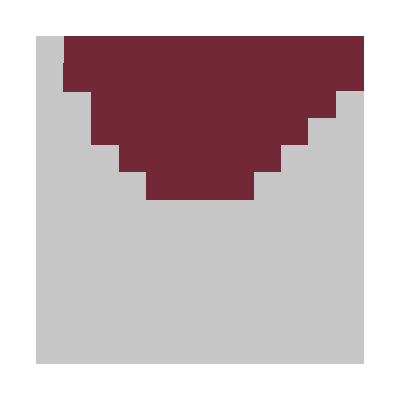
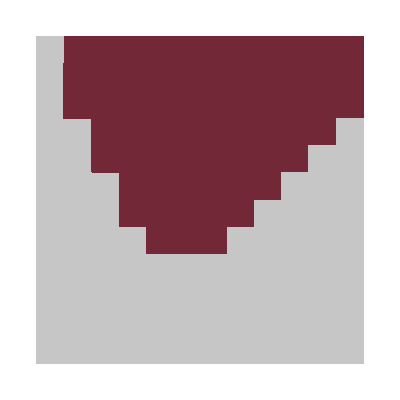
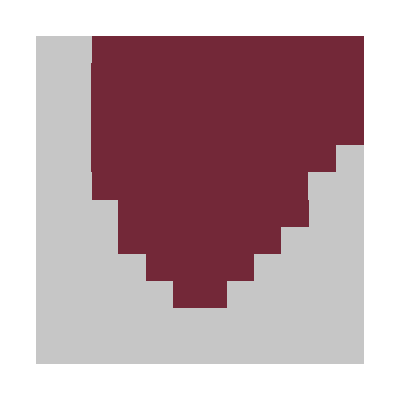
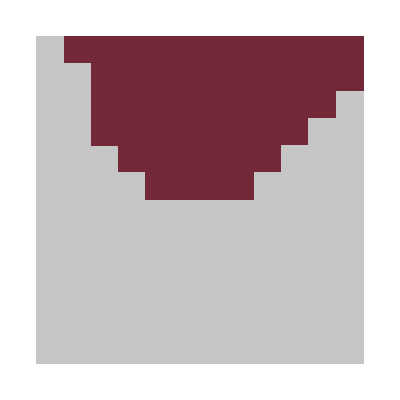
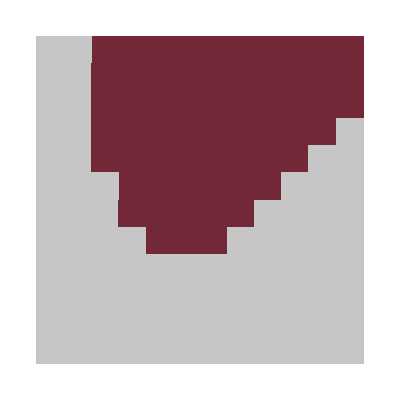
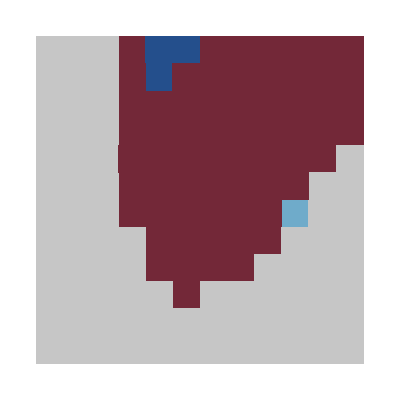
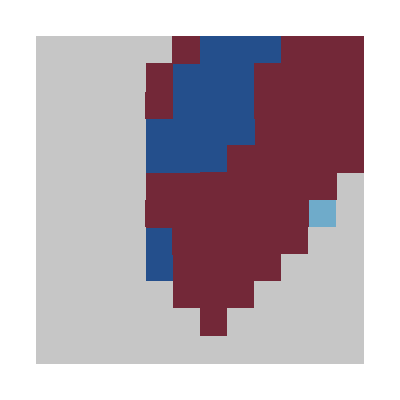
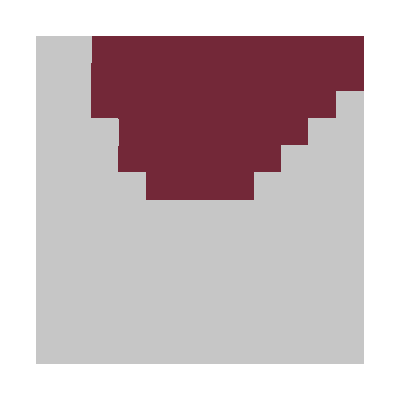
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
0.03 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.0948683 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.948683 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["kD = "<>ToString[#,TraditionalForm],Black]&/@(kD/4/.params)*10^Range[-1,0.5,0.5]]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@data,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@data,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@data,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@data,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-3}&/@Select[Flatten/@data,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-4,Darker@Gray,If[#==-3,White,If[#==-2,Darker@Darker@Green,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
]]/@Reverse@#&)/@analysisListMorph
]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"switchModelFinalParams-kDkdD-phaseDiagramSweeps-patternTypes.pdf",
Grid[
Transpose@Join[{Join[{Null},Style["kD = "<>ToString[#,TraditionalForm],Black]&/@(kD/4/.params)*10^Range[-1,0.5,0.5]]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@data,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@data,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@data,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@data,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-3}&/@Select[Flatten/@data,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-4,Darker@Gray,If[#==-3,White,If[#==-2,Darker@Darker@Green,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
]]/@Reverse@#&)/@analysisListMorph
]
]
]
];
```

### mu-kdD sweep

```mathematica
analysisListMorphMu=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-mu_"<>toString[mu]<>"-kdD_"<>toString[kdD]<>".h5"
},
Print["mu: ", mu," kdD: ", kdD/4];
testSweepMultipleFilesMorph[{filename
},"TimePoints"->Floor[1000/0.3]]
],{mu,{50,100}},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

mu: 50 kdD: 0.000474342

-Graphics-

period: 370.333, wavelength: 47.7143

{2.79794,2.19794}

-Graphics-

period: 256.385, wavelength: 41.75

{2.99794,2.39794}

-Graphics-

period: 666.6, wavelength: 55.6667

{3.19794,2.19794}

-Graphics-

period: 370.333, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 222.2, wavelength: 41.75

{3.19794,2.59794}

-Graphics-

period: 151.5, wavelength: 33.4

{3.19794,2.79794}

-Graphics-

period: 555.5, wavelength: 47.7143

{3.39794,2.39794}

-Graphics-

period: 333.3, wavelength: 41.75

{3.39794,2.59794}

-Graphics-

period: 208.313, wavelength: 37.1111

{3.39794,2.79794}

-Graphics-

period: 138.875, wavelength: 37.1111

{3.39794,2.99794}

-Graphics-

period: 666.6, wavelength: 55.6667

{3.59794,2.59794}

-Graphics-

period: 303., wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 185.167, wavelength: 27.8333

{3.59794,2.99794}

-Graphics-

period: 128.192, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 87.7105, wavelength: 27.8333

{3.59794,3.39794}

mu: 50 kdD: 0.0015

-Graphics-

period: 151.5, wavelength: 37.1111

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.59794,2.79794}

-Graphics-

period: 87.7105, wavelength: 30.3636

{2.59794,2.99794}

-Graphics-

period: 66.66, wavelength: 27.8333

{2.59794,3.19794}

-Graphics-

period: 333.3, wavelength: 41.75

{2.79794,2.19794}

-Graphics-

period: 222.2, wavelength: 37.1111

{2.79794,2.39794}

-Graphics-

period: 158.714, wavelength: 33.4

{2.79794,2.59794}

-Graphics-

period: 119.036, wavelength: 33.4

{2.79794,2.79794}

-Graphics-

period: 90.0811, wavelength: 30.3636

{2.79794,2.99794}

-Graphics-

period: 416.625, wavelength: 41.75

{2.99794,2.19794}

-Graphics-

period: 256.385, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 33.4

{2.99794,2.59794}

-Graphics-

period: 133.32, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 101., wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 370.333, wavelength: 41.75

{3.19794,2.39794}

-Graphics-

period: 222.2, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 151.5, wavelength: 27.8333

{3.19794,2.79794}

-Graphics-

period: 114.931, wavelength: 27.8333

{3.19794,2.99794}

-Graphics-

period: 87.7105, wavelength: 23.8571

{3.19794,3.19794}

-Graphics-

period: 65.3529, wavelength: 23.8571

{3.19794,3.39794}

-Graphics-

period: 333.3, wavelength: 41.75

{3.39794,2.59794}

-Graphics-

period: 196.059, wavelength: 37.1111

{3.39794,2.79794}

-Graphics-

period: 133.32, wavelength: 30.3636

{3.39794,2.99794}

-Graphics-

period: 98.0294, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 75.75, wavelength: 22.2667

{3.39794,3.39794}

-Graphics-

period: 59.5179, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 303., wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 185.167, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 114.931, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 83.325, wavelength: 20.875

{3.59794,3.39794}

-Graphics-

period: 65.3529, wavelength: 20.875

{3.59794,3.59794}

mu: 50 kdD: 0.00474342

-Graphics-

period: 158.714, wavelength: 33.4

{2.39794,2.59794}

-Graphics-

period: 119.036, wavelength: 30.3636

{2.39794,2.79794}

-Graphics-

period: 90.0811, wavelength: 27.8333

{2.39794,2.99794}

-Graphics-

period: 69.4375, wavelength: 25.6923

{2.39794,3.19794}

-Graphics-

period: 54.6393, wavelength: 27.8333

{2.39794,3.39794}

-Graphics-

period: 43.8553, wavelength: 25.6923

{2.39794,3.59794}

-Graphics-

period: 222.2, wavelength: 33.4

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 30.3636

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 25.6923

{2.59794,2.79794}

-Graphics-

period: 90.0811, wavelength: 23.8571

{2.59794,2.99794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{2.59794,3.19794}

-Graphics-

period: 56.4915, wavelength: 25.6923

{2.59794,3.39794}

-Graphics-

period: 44.44, wavelength: 23.8571

{2.59794,3.59794}

-Graphics-

period: 222.2, wavelength: 30.3636

{2.79794,2.39794}

-Graphics-

period: 158.714, wavelength: 27.8333

{2.79794,2.59794}

-Graphics-

period: 119.036, wavelength: 23.8571

{2.79794,2.79794}

-Graphics-

period: 92.5833, wavelength: 23.8571

{2.79794,2.99794}

-Graphics-

period: 74.0667, wavelength: 22.2667

{2.79794,3.19794}

-Graphics-

period: 59.5179, wavelength: 22.2667

{2.79794,3.39794}

-Graphics-

period: 47.6143, wavelength: 22.2667

{2.79794,3.59794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 175.421, wavelength: 27.8333

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 77.5116, wavelength: 20.875

{2.99794,3.19794}

-Graphics-

period: 62.8868, wavelength: 18.5556

{2.99794,3.39794}

-Graphics-

period: 51.2769, wavelength: 18.5556

{2.99794,3.59794}

-Graphics-

period: 238.071, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 151.5, wavelength: 33.4

{3.19794,2.79794}

-Graphics-

period: 107.516, wavelength: 23.8571

{3.19794,2.99794}

-Graphics-

period: 81.2927, wavelength: 20.875

{3.19794,3.19794}

-Graphics-

period: 65.3529, wavelength: 16.7

{3.19794,3.39794}

-Graphics-

period: 53.7581, wavelength: 17.5789

{3.19794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 128.192, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 90.0811, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 68.0204, wavelength: 18.5556

{3.39794,3.39794}

-Graphics-

period: 54.6393, wavelength: 15.1818

{3.39794,3.59794}

-Graphics-

period: 256.385, wavelength: 22.2667

inverted SW

{3.59794,2.99794}

-Graphics-

period: 111.1, wavelength: 30.3636

{3.59794,3.19794}

-Graphics-

period: 77.5116, wavelength: 27.8333

{3.59794,3.39794}

-Graphics-

period: 56.4915, wavelength: 15.9048

{3.59794,3.59794}

mu: 50 kdD: 0.015

-Graphics-

period: 98.0294, wavelength: 25.6923

{2.19794,2.99794}

-Graphics-

period: 74.0667, wavelength: 23.8571

{2.19794,3.19794}

-Graphics-

period: 58.4737, wavelength: 22.2667

{2.19794,3.39794}

-Graphics-

period: 46.2917, wavelength: 20.875

{2.19794,3.59794}

-Graphics-

period: 119.036, wavelength: 23.8571

{2.39794,2.79794}

-Graphics-

period: 90.0811, wavelength: 22.2667

{2.39794,2.99794}

-Graphics-

period: 70.9149, wavelength: 19.6471

{2.39794,3.19794}

-Graphics-

period: 56.4915, wavelength: 20.875

{2.39794,3.39794}

-Graphics-

period: 45.6575, wavelength: 18.5556

{2.39794,3.59794}

-Graphics-

period: 158.714, wavelength: 27.8333

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 23.8571

{2.59794,2.79794}

-Graphics-

period: 90.0811, wavelength: 20.875

{2.59794,2.99794}

-Graphics-

period: 70.9149, wavelength: 18.5556

{2.59794,3.19794}

-Graphics-

period: 57.4655, wavelength: 17.5789

{2.59794,3.39794}

-Graphics-

period: 46.9437, wavelength: 18.5556

{2.59794,3.59794}

-Graphics-

period: 166.65, wavelength: 30.3636

{2.79794,2.59794}

-Graphics-

period: 119.036, wavelength: 25.6923

{2.79794,2.79794}

-Graphics-

period: 90.0811, wavelength: 18.5556

{2.79794,2.99794}

-Graphics-

period: 70.9149, wavelength: 16.7

{2.79794,3.19794}

-Graphics-

period: 57.4655, wavelength: 16.7

{2.79794,3.39794}

-Graphics-

period: 47.6143, wavelength: 15.9048

{2.79794,3.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 92.5833, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 70.9149, wavelength: 17.5789

{2.99794,3.19794}

-Graphics-

period: 57.4655, wavelength: 15.9048

{2.99794,3.39794}

-Graphics-

period: 47.6143, wavelength: 15.1818

{2.99794,3.59794}

-Graphics-

period: 151.5, wavelength: 20.875

inverted SW

{3.19794,2.79794}

-Graphics-

period: 104.156, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 75.75, wavelength: 22.2667

{3.19794,3.19794}

-Graphics-

period: 58.4737, wavelength: 16.7

{3.19794,3.39794}

-Graphics-

period: 46.9437, wavelength: 15.9048

{3.19794,3.59794}

-Graphics-

period: 138.875, wavelength: 15.9048

inverted SW

{3.39794,2.99794}

-Graphics-

period: 85.4615, wavelength: 23.8571

{3.39794,3.19794}

-Graphics-

period: 62.8868, wavelength: 19.6471

{3.39794,3.39794}

-Graphics-

period: 48.3043, wavelength: 19.6471

{3.39794,3.59794}

-Graphics-

period: 72.4565, wavelength: 20.875

{3.59794,3.39794}

-Graphics-

period: 52.9048, wavelength: 20.875

{3.59794,3.59794}

mu: 50 kdD: 0.0474342

-Graphics-

period: 59.5179, wavelength: 16.7

{2.19794,3.39794}

-Graphics-

period: 46.9437, wavelength: 16.7

{2.19794,3.59794}

-Graphics-

period: 70.9149, wavelength: 16.7

{2.39794,3.19794}

-Graphics-

period: 55.55, wavelength: 15.9048

{2.39794,3.39794}

-Graphics-

period: 45.0405, wavelength: 15.9048

{2.39794,3.59794}

-Graphics-

period: 90.0811, wavelength: 19.6471

{2.59794,2.99794}

-Graphics-

period: 66.66, wavelength: 17.5789

{2.59794,3.19794}

-Graphics-

period: 53.7581, wavelength: 14.5217

{2.59794,3.39794}

-Graphics-

period: 43.2857, wavelength: 13.9167

{2.59794,3.59794}

-Graphics-

period: 87.7105, wavelength: 22.2667

{2.79794,2.99794}

-Graphics-

period: 65.3529, wavelength: 18.5556

{2.79794,3.19794}

-Graphics-

period: 52.0781, wavelength: 14.5217

{2.79794,3.39794}

-Graphics-

period: 42.1899, wavelength: 12.8462

{2.79794,3.59794}

-Graphics-

period: 85.4615, wavelength: 13.9167

inverted SW

{2.99794,2.99794}

-Graphics-

period: 68.0204, wavelength: 18.5556

{2.99794,3.19794}

-Graphics-

period: 52.0781, wavelength: 17.5789

{2.99794,3.39794}

-Graphics-

period: 41.6625, wavelength: 14.5217

{2.99794,3.59794}

-Graphics-

period: 72.4565, wavelength: 20.875

{3.19794,3.19794}

-Graphics-

period: 53.7581, wavelength: 16.7

{3.19794,3.39794}

-Graphics-

period: 42.1899, wavelength: 16.7

{3.19794,3.59794}

-Graphics-

period: 85.4615, wavelength: 10.7742

inverted SW

{3.39794,3.19794}

-Graphics-

period: 59.5179, wavelength: 11.9286

{3.39794,3.39794}

-Graphics-

period: 43.2857, wavelength: 15.9048

{3.39794,3.59794}

-Graphics-

period: 74.0667, wavelength: 5.3871

{3.59794,3.39794}

-Graphics-

period: 44.44, wavelength: 9.54286

inverted SW

{3.59794,3.59794}

mu: 100 kdD: 0.000474342

-Graphics-

period: 277.75, wavelength: 47.7143

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 41.75

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 37.1111

{2.99794,2.79794}

-Graphics-

period: 95.2286, wavelength: 33.4

{2.99794,2.99794}

-Graphics-

period: 70.9149, wavelength: 30.3636

{2.99794,3.19794}

-Graphics-

period: 370.333, wavelength: 47.7143

{3.19794,2.39794}

-Graphics-

period: 222.2, wavelength: 41.75

{3.19794,2.59794}

-Graphics-

period: 151.5, wavelength: 37.1111

{3.19794,2.79794}

-Graphics-

period: 107.516, wavelength: 30.3636

{3.19794,2.99794}

-Graphics-

period: 79.3571, wavelength: 27.8333

{3.19794,3.19794}

-Graphics-

period: 833.25, wavelength: 47.7143

{3.39794,2.39794}

-Graphics-

period: 303., wavelength: 41.75

{3.39794,2.59794}

-Graphics-

period: 196.059, wavelength: 33.4

{3.39794,2.79794}

-Graphics-

period: 128.192, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 92.5833, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 68.0204, wavelength: 25.6923

{3.39794,3.39794}

-Graphics-

period: 1111., wavelength: 55.6667

inverted SW

{3.59794,2.59794}

-Graphics-

period: 303., wavelength: 41.75

{3.59794,2.79794}

-Graphics-

period: 175.421, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 114.931, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 83.325, wavelength: 25.6923

{3.59794,3.39794}

mu: 100 kdD: 0.0015

-Graphics-

period: 175.421, wavelength: 37.1111

{2.79794,2.59794}

-Graphics-

period: 123.444, wavelength: 30.3636

{2.79794,2.79794}

-Graphics-

period: 92.5833, wavelength: 27.8333

{2.79794,2.99794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{2.79794,3.19794}

-Graphics-

period: 55.55, wavelength: 23.8571

{2.79794,3.39794}

-Graphics-

period: 43.2857, wavelength: 25.6923

{2.79794,3.59794}

-Graphics-

period: 277.75, wavelength: 37.1111

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 37.1111

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{2.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 27.8333

{2.99794,2.99794}

-Graphics-

period: 75.75, wavelength: 23.8571

{2.99794,3.19794}

-Graphics-

period: 58.4737, wavelength: 23.8571

{2.99794,3.39794}

-Graphics-

period: 222.2, wavelength: 37.1111

{3.19794,2.59794}

-Graphics-

period: 151.5, wavelength: 27.8333

{3.19794,2.79794}

-Graphics-

period: 107.516, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 83.325, wavelength: 23.8571

{3.19794,3.19794}

-Graphics-

period: 64.0962, wavelength: 20.875

{3.19794,3.39794}

-Graphics-

period: 49.7463, wavelength: 19.6471

{3.19794,3.59794}

-Graphics-

period: 476.143, wavelength: 37.1111

inverted SW

{3.39794,2.59794}

-Graphics-

period: 196.059, wavelength: 37.1111

{3.39794,2.79794}

-Graphics-

period: 128.192, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 92.5833, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 70.9149, wavelength: 19.6471

{3.39794,3.39794}

-Graphics-

period: 56.4915, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 175.421, wavelength: 33.4

{3.59794,2.99794}

-Graphics-

period: 111.1, wavelength: 27.8333

{3.59794,3.19794}

-Graphics-

period: 79.3571, wavelength: 18.5556

{3.59794,3.39794}

-Graphics-

period: 61.7222, wavelength: 17.5789

{3.59794,3.59794}

mu: 100 kdD: 0.00474342

-Graphics-

period: 128.192, wavelength: 27.8333

{2.59794,2.79794}

-Graphics-

period: 95.2286, wavelength: 25.6923

{2.59794,2.99794}

-Graphics-

period: 74.0667, wavelength: 22.2667

{2.59794,3.19794}

-Graphics-

period: 57.4655, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 45.6575, wavelength: 22.2667

{2.59794,3.59794}

-Graphics-

period: 185.167, wavelength: 27.8333

{2.79794,2.59794}

-Graphics-

period: 128.192, wavelength: 30.3636

{2.79794,2.79794}

-Graphics-

period: 95.2286, wavelength: 22.2667

{2.79794,2.99794}

-Graphics-

period: 74.0667, wavelength: 20.875

{2.79794,3.19794}

-Graphics-

period: 58.4737, wavelength: 20.875

{2.79794,3.39794}

-Graphics-

period: 46.9437, wavelength: 19.6471

{2.79794,3.59794}

-Graphics-

period: 196.059, wavelength: 30.3636

{2.99794,2.59794}

-Graphics-

period: 133.32, wavelength: 23.8571

{2.99794,2.79794}

-Graphics-

period: 98.0294, wavelength: 19.6471

{2.99794,2.99794}

-Graphics-

period: 75.75, wavelength: 18.5556

{2.99794,3.19794}

-Graphics-

period: 60.6, wavelength: 17.5789

{2.99794,3.39794}

-Graphics-

period: 49.0147, wavelength: 17.5789

{2.99794,3.59794}

-Graphics-

period: 151.5, wavelength: 25.6923

{3.19794,2.79794}

-Graphics-

period: 104.156, wavelength: 25.6923

{3.19794,2.99794}

-Graphics-

period: 79.3571, wavelength: 18.5556

{3.19794,3.19794}

-Graphics-

period: 62.8868, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 50.5, wavelength: 15.1818

{3.19794,3.59794}

-Graphics-

period: 128.192, wavelength: 27.8333

{3.39794,2.99794}

-Graphics-

period: 87.7105, wavelength: 25.6923

{3.39794,3.19794}

-Graphics-

period: 65.3529, wavelength: 15.9048

{3.39794,3.39794}

-Graphics-

period: 52.0781, wavelength: 14.5217

{3.39794,3.59794}

-Graphics-

period: 111.1, wavelength: 25.6923

{3.59794,3.19794}

-Graphics-

period: 74.0667, wavelength: 25.6923

{3.59794,3.39794}

-Graphics-

period: 54.6393, wavelength: 15.1818

{3.59794,3.59794}

mu: 100 kdD: 0.015

-Graphics-

period: 61.7222, wavelength: 18.5556

{2.39794,3.39794}

-Graphics-

period: 48.3043, wavelength: 17.5789

{2.39794,3.59794}

-Graphics-

period: 101., wavelength: 20.875

inverted SW

{2.59794,2.99794}

-Graphics-

period: 74.0667, wavelength: 18.5556

{2.59794,3.19794}

-Graphics-

period: 58.4737, wavelength: 18.5556

{2.59794,3.39794}

-Graphics-

period: 46.9437, wavelength: 15.1818

{2.59794,3.59794}

-Graphics-

period: 95.2286, wavelength: 18.5556

{2.79794,2.99794}

-Graphics-

period: 72.4565, wavelength: 16.7

{2.79794,3.19794}

-Graphics-

period: 57.4655, wavelength: 15.1818

{2.79794,3.39794}

-Graphics-

period: 46.2917, wavelength: 13.9167

{2.79794,3.59794}

-Graphics-

period: 98.0294, wavelength: 23.8571

{2.99794,2.99794}

-Graphics-

period: 72.4565, wavelength: 14.5217

{2.99794,3.19794}

-Graphics-

period: 57.4655, wavelength: 13.9167

{2.99794,3.39794}

-Graphics-

period: 46.2917, wavelength: 15.1818

{2.99794,3.59794}

-Graphics-

period: 107.516, wavelength: 27.8333

{3.19794,2.99794}

-Graphics-

period: 75.75, wavelength: 14.5217

{3.19794,3.19794}

-Graphics-

period: 58.4737, wavelength: 14.5217

{3.19794,3.39794}

-Graphics-

period: 46.2917, wavelength: 12.3704

{3.19794,3.59794}

-Graphics-

period: 87.7105, wavelength: 22.2667

{3.39794,3.19794}

-Graphics-

period: 62.8868, wavelength: 12.8462

{3.39794,3.39794}

-Graphics-

period: 47.6143, wavelength: 17.5789

{3.39794,3.59794}

-Graphics-

period: 70.9149, wavelength: 12.3704

inverted SW

{3.59794,3.39794}

-Graphics-

period: 50.5, wavelength: 17.5789

{3.59794,3.59794}

mu: 100 kdD: 0.0474342

-Graphics-

period: 46.9437, wavelength: 11.9286

{2.59794,3.59794}

-Graphics-

period: 57.4655, wavelength: 11.9286

{2.79794,3.39794}

-Graphics-

period: 44.44, wavelength: 10.7742

{2.79794,3.59794}

-Graphics-

period: 57.4655, wavelength: 11.1333

{2.99794,3.39794}

-Graphics-

period: 43.2857, wavelength: 12.3704

{2.99794,3.59794}

-Graphics-

period: 60.6, wavelength: 10.4375

{3.19794,3.39794}

-Graphics-

period: 44.44, wavelength: 9.27778

{3.19794,3.59794}

-Graphics-

period: 53.7581, wavelength: 11.5172

inverted SW

{3.39794,3.39794}

-Graphics-

period: 41.6625, wavelength: 9.54286

inverted SW

{3.39794,3.59794}

-Graphics-

period: 42.7308, wavelength: 4.84058

{3.59794,3.59794}

```mathematica
analysisListMorphMuFull=Join[{analysisListMorph[[3]]},analysisListMorphMu];
```

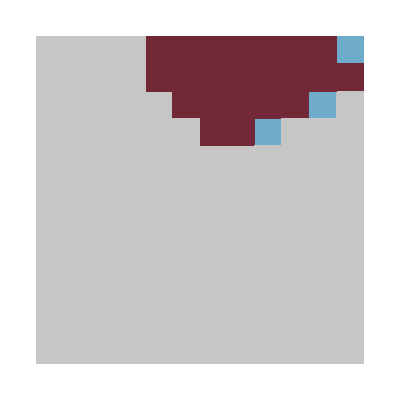
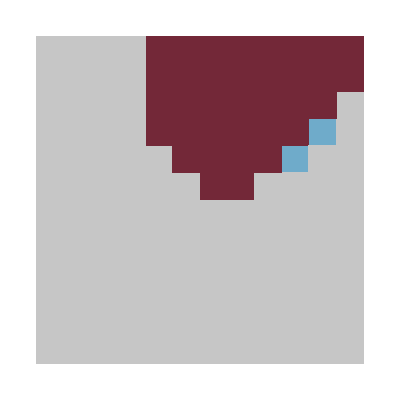
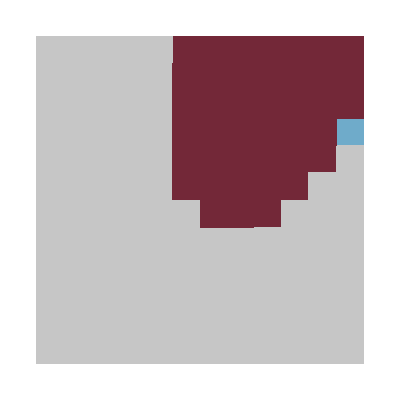
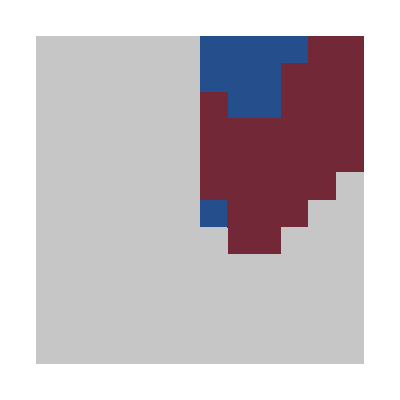
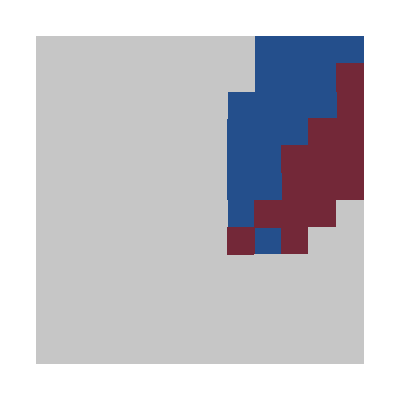
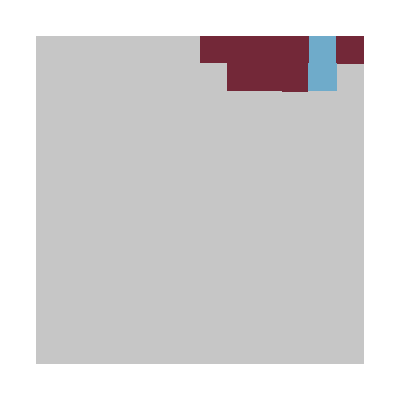
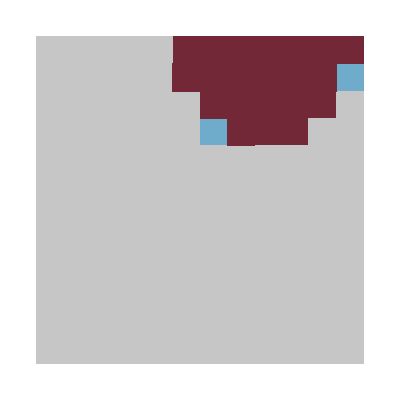
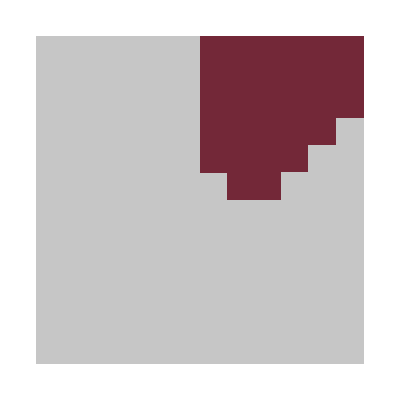
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
μ = 20 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
μ = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["μ = "<>ToString[#,TraditionalForm],Black]&/@{20,50,100}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@data,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@data,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@data,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@data,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-3}&/@Select[Flatten/@data,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-4,Darker@Gray,If[#==-3,White,If[#==-2,Darker@Darker@Green,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
]]/@Reverse@#&)/@analysisListMorphMuFull
]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"switchModelFinalParams-mukdD-phaseDiagramSweeps-patternTypes.pdf",
Grid[
Transpose@Join[{Join[{Null},Style["μ = "<>ToString[#,TraditionalForm],Black]&/@{20,50,100}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@data,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@data,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@data,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@data,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-3}&/@Select[Flatten/@data,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-4,Darker@Gray,If[#==-3,White,If[#==-2,Darker@Darker@Green,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
]]/@Reverse@#&)/@analysisListMorphMuFull
]
]
]
];
```

### DdDde-kdD sweep (not included in the article)

```mathematica
analysisListMorphDdDde=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-DdDde_"<>toString[mu]<>"-kdD_"<>toString[kdD]<>".h5"
},
Print["mu: ", mu," kdD: ", kdD/4];
testSweepMultipleFilesMorph[{filename
},"TimePoints"->Floor[1000/0.3]]
],{mu,{0.01,0.1}},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

mu: 0.01 kdD: 0.000474342

-Graphics-

period: 238.071, wavelength: 37.1111

{2.39794,2.19794}

-Graphics-

period: 175.421, wavelength: 37.1111

{2.39794,2.39794}

-Graphics-

period: 138.875, wavelength: 37.1111

{2.39794,2.59794}

-Graphics-

period: 1111., wavelength: 41.75

{3.39794,1.99794}

-Graphics-

period: 666.6, wavelength: 37.1111

{3.39794,2.19794}

-Graphics-

period: 1111., wavelength: 41.75

{3.59794,2.19794}

-Graphics-

period: 666.6, wavelength: 25.6923

{3.59794,2.39794}

mu: 0.01 kdD: 0.0015

-Graphics-

period: 222.2, wavelength: 33.4

{2.19794,2.19794}

-Graphics-

period: 416.625, wavelength: 33.4

{2.59794,1.79794}

-Graphics-

period: 833.25, wavelength: 33.4

{2.79794,1.59794}

-Graphics-

period: 666.6, wavelength: 33.4

{2.99794,1.79794}

-Graphics-

period: 476.143, wavelength: 33.4

{2.99794,1.99794}

-Graphics-

period: 1111., wavelength: 30.3636

{3.19794,1.79794}

-Graphics-

period: 666.6, wavelength: 33.4

{3.19794,1.99794}

-Graphics-

period: 476.143, wavelength: 25.6923

{3.19794,2.19794}

-Graphics-

period: 81.2927, wavelength: 11.1333

{3.19794,3.19794}

-Graphics-

period: 64.0962, wavelength: 10.4375

{3.19794,3.39794}

-Graphics-

period: 1666.5, wavelength: 33.4

{3.39794,1.99794}

-Graphics-

period: 666.6, wavelength: 27.8333

{3.39794,2.19794}

-Graphics-

period: 416.625, wavelength: 25.6923

{3.39794,2.39794}

-Graphics-

period: 303., wavelength: 25.6923

{3.39794,2.59794}

-Graphics-

period: 208.313, wavelength: 27.8333

{3.39794,2.79794}

-Graphics-

period: 144.913, wavelength: 25.6923

{3.39794,2.99794}

-Graphics-

period: 666.6, wavelength: 27.8333

{3.59794,2.39794}

-Graphics-

period: 416.625, wavelength: 30.3636

{3.59794,2.59794}

-Graphics-

period: 277.75, wavelength: 23.8571

{3.59794,2.79794}

-Graphics-

period: 196.059, wavelength: 25.6923

{3.59794,2.99794}

-Graphics-

period: 133.32, wavelength: 23.8571

{3.59794,3.19794}

-Graphics-

period: 95.2286, wavelength: 22.2667

{3.59794,3.39794}

mu: 0.01 kdD: 0.00474342

-Graphics-

period: 175.421, wavelength: 30.3636

{1.99794,2.39794}

-Graphics-

period: 555.5, wavelength: 30.3636

{2.39794,1.59794}

-Graphics-

period: 303., wavelength: 27.8333

{2.39794,1.99794}

-Graphics-

period: 666.6, wavelength: 27.8333

{2.59794,1.59794}

-Graphics-

period: 476.143, wavelength: 30.3636

{2.59794,1.79794}

-Graphics-

period: 333.3, wavelength: 22.2667

{2.59794,1.99794}

-Graphics-

period: 238.071, wavelength: 30.3636

{2.59794,2.19794}

-Graphics-

period: 1111., wavelength: 27.8333

{2.79794,1.59794}

-Graphics-

period: 555.5, wavelength: 27.8333

{2.79794,1.79794}

-Graphics-

period: 370.333, wavelength: 27.8333

{2.79794,1.99794}

-Graphics-

period: 277.75, wavelength: 25.6923

{2.79794,2.19794}

-Graphics-

period: 208.313, wavelength: 27.8333

{2.79794,2.39794}

-Graphics-

period: 833.25, wavelength: 23.8571

{2.99794,1.79794}

-Graphics-

period: 476.143, wavelength: 25.6923

{2.99794,1.99794}

-Graphics-

period: 333.3, wavelength: 20.875

{2.99794,2.19794}

-Graphics-

period: 238.071, wavelength: 23.8571

{2.99794,2.39794}

-Graphics-

period: 185.167, wavelength: 25.6923

{2.99794,2.59794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.99794,2.79794}

-Graphics-

period: 107.516, wavelength: 22.2667

{2.99794,2.99794}

-Graphics-

period: 1666.5, wavelength: 27.8333

{3.19794,1.99794}

-Graphics-

period: 416.625, wavelength: 22.2667

{3.19794,2.19794}

-Graphics-

period: 303., wavelength: 19.6471

{3.19794,2.39794}

-Graphics-

period: 208.313, wavelength: 22.2667

{3.19794,2.59794}

-Graphics-

period: 158.714, wavelength: 22.2667

{3.19794,2.79794}

-Graphics-

period: 123.444, wavelength: 18.5556

{3.19794,2.99794}

-Graphics-

period: 95.2286, wavelength: 20.875

{3.19794,3.19794}

-Graphics-

period: 74.0667, wavelength: 19.6471

{3.19794,3.39794}

-Graphics-

period: 416.625, wavelength: 18.5556

{3.39794,2.39794}

-Graphics-

period: 256.385, wavelength: 19.6471

{3.39794,2.59794}

-Graphics-

period: 185.167, wavelength: 17.5789

{3.39794,2.79794}

-Graphics-

period: 138.875, wavelength: 20.875

{3.39794,2.99794}

-Graphics-

period: 104.156, wavelength: 19.6471

{3.39794,3.19794}

-Graphics-

period: 81.2927, wavelength: 20.875

{3.39794,3.39794}

-Graphics-

period: 65.3529, wavelength: 19.6471

{3.39794,3.59794}

-Graphics-

period: 370.333, wavelength: 25.6923

{3.59794,2.59794}

-Graphics-

period: 238.071, wavelength: 19.6471

{3.59794,2.79794}

-Graphics-

period: 166.65, wavelength: 20.875

{3.59794,2.99794}

-Graphics-

period: 123.444, wavelength: 18.5556

{3.59794,3.19794}

-Graphics-

period: 92.5833, wavelength: 19.6471

{3.59794,3.39794}

-Graphics-

period: 70.9149, wavelength: 19.6471

{3.59794,3.59794}

mu: 0.01 kdD: 0.015

-Graphics-

period: 114.931, wavelength: 27.8333

{1.79794,2.79794}

-Graphics-

period: 87.7105, wavelength: 25.6923

{1.79794,2.99794}

-Graphics-

period: 175.421, wavelength: 25.6923

{1.99794,2.39794}

-Graphics-

period: 303., wavelength: 22.2667

{2.19794,1.99794}

-Graphics-

period: 222.2, wavelength: 23.8571

{2.19794,2.19794}

-Graphics-

period: 175.421, wavelength: 20.875

{2.19794,2.39794}

-Graphics-

period: 138.875, wavelength: 25.6923

{2.19794,2.59794}

-Graphics-

period: 107.516, wavelength: 20.875

{2.19794,2.79794}

-Graphics-

period: 416.625, wavelength: 20.875

{2.39794,1.79794}

-Graphics-

period: 303., wavelength: 22.2667

{2.39794,1.99794}

-Graphics-

period: 222.2, wavelength: 20.875

{2.39794,2.19794}

-Graphics-

period: 175.421, wavelength: 20.875

{2.39794,2.39794}

-Graphics-

period: 138.875, wavelength: 23.8571

{2.39794,2.59794}

-Graphics-

period: 111.1, wavelength: 22.2667

{2.39794,2.79794}

-Graphics-

period: 87.7105, wavelength: 22.2667

{2.39794,2.99794}

-Graphics-

period: 70.9149, wavelength: 23.8571

{2.39794,3.19794}

-Graphics-

period: 476.143, wavelength: 27.8333

{2.59794,1.79794}

-Graphics-

period: 303., wavelength: 20.875

{2.59794,1.99794}

-Graphics-

period: 238.071, wavelength: 20.875

{2.59794,2.19794}

-Graphics-

period: 185.167, wavelength: 19.6471

{2.59794,2.39794}

-Graphics-

period: 144.913, wavelength: 22.2667

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 20.875

{2.59794,2.79794}

-Graphics-

period: 92.5833, wavelength: 23.8571

{2.59794,2.99794}

-Graphics-

period: 75.75, wavelength: 22.2667

{2.59794,3.19794}

-Graphics-

period: 61.7222, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 50.5, wavelength: 19.6471

{2.59794,3.59794}

-Graphics-

period: 370.333, wavelength: 19.6471

{2.79794,1.99794}

-Graphics-

period: 256.385, wavelength: 22.2667

{2.79794,2.19794}

-Graphics-

period: 196.059, wavelength: 17.5789

{2.79794,2.39794}

-Graphics-

period: 151.5, wavelength: 19.6471

{2.79794,2.59794}

-Graphics-

period: 119.036, wavelength: 19.6471

{2.79794,2.79794}

-Graphics-

period: 95.2286, wavelength: 20.875

{2.79794,2.99794}

-Graphics-

period: 77.5116, wavelength: 18.5556

{2.79794,3.19794}

-Graphics-

period: 64.0962, wavelength: 18.5556

{2.79794,3.39794}

-Graphics-

period: 52.9048, wavelength: 18.5556

{2.79794,3.59794}

-Graphics-

period: 303., wavelength: 18.5556

{2.99794,2.19794}

-Graphics-

period: 222.2, wavelength: 16.7

{2.99794,2.39794}

-Graphics-

period: 166.65, wavelength: 16.7

{2.99794,2.59794}

-Graphics-

period: 128.192, wavelength: 17.5789

{2.99794,2.79794}

-Graphics-

period: 101., wavelength: 18.5556

{2.99794,2.99794}

-Graphics-

period: 81.2927, wavelength: 16.7

{2.99794,3.19794}

-Graphics-

period: 66.66, wavelength: 15.9048

{2.99794,3.39794}

-Graphics-

period: 54.6393, wavelength: 17.5789

{2.99794,3.59794}

-Graphics-

period: 277.75, wavelength: 19.6471

{3.19794,2.39794}

-Graphics-

period: 185.167, wavelength: 17.5789

{3.19794,2.59794}

-Graphics-

period: 138.875, wavelength: 16.7

{3.19794,2.79794}

-Graphics-

period: 107.516, wavelength: 16.7

{3.19794,2.99794}

-Graphics-

period: 85.4615, wavelength: 17.5789

{3.19794,3.19794}

-Graphics-

period: 69.4375, wavelength: 15.9048

{3.19794,3.39794}

-Graphics-

period: 56.4915, wavelength: 16.7

{3.19794,3.59794}

-Graphics-

period: 238.071, wavelength: 19.6471

{3.39794,2.59794}

-Graphics-

period: 158.714, wavelength: 13.9167

{3.39794,2.79794}

-Graphics-

period: 119.036, wavelength: 14.5217

{3.39794,2.99794}

-Graphics-

period: 92.5833, wavelength: 15.1818

{3.39794,3.19794}

-Graphics-

period: 72.4565, wavelength: 16.7

{3.39794,3.39794}

-Graphics-

period: 59.5179, wavelength: 15.9048

{3.39794,3.59794}

-Graphics-

period: 144.913, wavelength: 15.9048

{3.59794,2.99794}

-Graphics-

period: 101., wavelength: 16.7

{3.59794,3.19794}

-Graphics-

period: 77.5116, wavelength: 14.5217

{3.59794,3.39794}

-Graphics-

period: 61.7222, wavelength: 14.5217

{3.59794,3.59794}

mu: 0.01 kdD: 0.0474342

-Graphics-

period: 114.931, wavelength: 20.875

{1.79794,2.79794}

-Graphics-

period: 90.0811, wavelength: 19.6471

{1.79794,2.99794}

-Graphics-

period: 70.9149, wavelength: 19.6471

{1.79794,3.19794}

-Graphics-

period: 56.4915, wavelength: 19.6471

{1.79794,3.39794}

-Graphics-

period: 45.0405, wavelength: 19.6471

{1.79794,3.59794}

-Graphics-

period: 175.421, wavelength: 18.5556

{1.99794,2.39794}

-Graphics-

period: 138.875, wavelength: 19.6471

{1.99794,2.59794}

-Graphics-

period: 107.516, wavelength: 18.5556

{1.99794,2.79794}

-Graphics-

period: 85.4615, wavelength: 19.6471

{1.99794,2.99794}

-Graphics-

period: 68.0204, wavelength: 20.875

{1.99794,3.19794}

-Graphics-

period: 55.55, wavelength: 19.6471

{1.99794,3.39794}

-Graphics-

period: 45.0405, wavelength: 20.875

{1.99794,3.59794}

-Graphics-

period: 222.2, wavelength: 19.6471

{2.19794,2.19794}

-Graphics-

period: 166.65, wavelength: 17.5789

{2.19794,2.39794}

-Graphics-

period: 128.192, wavelength: 18.5556

{2.19794,2.59794}

-Graphics-

period: 104.156, wavelength: 18.5556

{2.19794,2.79794}

-Graphics-

period: 83.325, wavelength: 16.7

{2.19794,2.99794}

-Graphics-

period: 68.0204, wavelength: 17.5789

{2.19794,3.19794}

-Graphics-

period: 55.55, wavelength: 19.6471

{2.19794,3.39794}

-Graphics-

period: 45.6575, wavelength: 19.6471

{2.19794,3.59794}

-Graphics-

period: 208.313, wavelength: 19.6471

{2.39794,2.19794}

-Graphics-

period: 166.65, wavelength: 17.5789

{2.39794,2.39794}

-Graphics-

period: 128.192, wavelength: 15.9048

{2.39794,2.59794}

-Graphics-

period: 101., wavelength: 15.9048

{2.39794,2.79794}

-Graphics-

period: 83.325, wavelength: 17.5789

{2.39794,2.99794}

-Graphics-

period: 68.0204, wavelength: 17.5789

{2.39794,3.19794}

-Graphics-

period: 55.55, wavelength: 16.7

{2.39794,3.39794}

-Graphics-

period: 46.2917, wavelength: 17.5789

{2.39794,3.59794}

-Graphics-

period: 222.2, wavelength: 15.9048

{2.59794,2.19794}

-Graphics-

period: 166.65, wavelength: 14.5217

{2.59794,2.39794}

-Graphics-

period: 128.192, wavelength: 15.1818

{2.59794,2.59794}

-Graphics-

period: 101., wavelength: 15.1818

{2.59794,2.79794}

-Graphics-

period: 83.325, wavelength: 15.9048

{2.59794,2.99794}

-Graphics-

period: 68.0204, wavelength: 15.1818

{2.59794,3.19794}

-Graphics-

period: 56.4915, wavelength: 13.9167

{2.59794,3.39794}

-Graphics-

period: 46.9437, wavelength: 14.5217

{2.59794,3.59794}

-Graphics-

period: 238.071, wavelength: 17.5789

{2.79794,2.19794}

-Graphics-

period: 175.421, wavelength: 15.1818

{2.79794,2.39794}

-Graphics-

period: 133.32, wavelength: 12.3704

{2.79794,2.59794}

-Graphics-

period: 104.156, wavelength: 15.1818

{2.79794,2.79794}

-Graphics-

period: 83.325, wavelength: 13.36

{2.79794,2.99794}

-Graphics-

period: 68.0204, wavelength: 15.9048

{2.79794,3.19794}

-Graphics-

period: 56.4915, wavelength: 14.5217

{2.79794,3.39794}

-Graphics-

period: 47.6143, wavelength: 14.5217

{2.79794,3.59794}

-Graphics-

period: 196.059, wavelength: 15.1818

{2.99794,2.39794}

-Graphics-

period: 144.913, wavelength: 13.9167

{2.99794,2.59794}

-Graphics-

period: 107.516, wavelength: 13.36

{2.99794,2.79794}

-Graphics-

period: 85.4615, wavelength: 13.36

{2.99794,2.99794}

-Graphics-

period: 69.4375, wavelength: 13.9167

{2.99794,3.19794}

-Graphics-

period: 57.4655, wavelength: 15.1818

{2.99794,3.39794}

-Graphics-

period: 48.3043, wavelength: 12.3704

{2.99794,3.59794}

-Graphics-

period: 119.036, wavelength: 13.36

{3.19794,2.79794}

-Graphics-

period: 90.0811, wavelength: 11.9286

{3.19794,2.99794}

-Graphics-

period: 70.9149, wavelength: 12.3704

{3.19794,3.19794}

-Graphics-

period: 58.4737, wavelength: 11.1333

{3.19794,3.39794}

-Graphics-

period: 49.0147, wavelength: 13.9167

{3.19794,3.59794}

-Graphics-

period: 101., wavelength: 12.3704

{3.39794,2.99794}

-Graphics-

period: 75.75, wavelength: 11.9286

{3.39794,3.19794}

-Graphics-

period: 59.5179, wavelength: 10.7742

{3.39794,3.39794}

-Graphics-

period: 49.0147, wavelength: 13.36

{3.39794,3.59794}

-Graphics-

period: 90.0811, wavelength: 13.9167

{3.59794,3.19794}

-Graphics-

period: 64.0962, wavelength: 12.3704

{3.59794,3.39794}

-Graphics-

period: 50.5, wavelength: 11.1333

{3.59794,3.59794}

mu: 0.1 kdD: 0.000474342

-Graphics-

period: 1666.5, wavelength: 83.5

{3.19794,2.19794}

-Graphics-

period: 555.5, wavelength: 55.6667

{3.19794,2.39794}

-Graphics-

period: 303., wavelength: 47.7143

{3.19794,2.59794}

-Graphics-

period: 1666.5, wavelength: 33.4

{3.39794,2.39794}

-Graphics-

period: 476.143, wavelength: 55.6667

{3.39794,2.59794}

-Graphics-

period: 256.385, wavelength: 47.7143

{3.39794,2.79794}

-Graphics-

period: 476.143, wavelength: 55.6667

{3.59794,2.79794}

-Graphics-

period: 238.071, wavelength: 41.75

{3.59794,2.99794}

-Graphics-

period: 151.5, wavelength: 41.75

{3.59794,3.19794}

-Graphics-

period: 98.0294, wavelength: 37.1111

{3.59794,3.39794}

mu: 0.1 kdD: 0.0015

-Graphics-

period: 303., wavelength: 55.6667

{2.39794,2.19794}

-Graphics-

period: 208.313, wavelength: 55.6667

{2.39794,2.39794}

-Graphics-

period: 555.5, wavelength: 66.8

{2.59794,1.99794}

-Graphics-

period: 303., wavelength: 55.6667

{2.59794,2.19794}

-Graphics-

period: 208.313, wavelength: 47.7143

{2.59794,2.39794}

-Graphics-

period: 151.5, wavelength: 41.75

{2.59794,2.59794}

-Graphics-

period: 833.25, wavelength: 66.8

{2.79794,1.99794}

-Graphics-

period: 370.333, wavelength: 55.6667

{2.79794,2.19794}

-Graphics-

period: 256.385, wavelength: 47.7143

{2.79794,2.39794}

-Graphics-

period: 175.421, wavelength: 41.75

{2.79794,2.59794}

-Graphics-

period: 128.192, wavelength: 37.1111

{2.79794,2.79794}

-Graphics-

period: 666.6, wavelength: 66.8

{2.99794,2.19794}

-Graphics-

period: 333.3, wavelength: 55.6667

{2.99794,2.39794}

-Graphics-

period: 208.313, wavelength: 37.1111

{2.99794,2.59794}

-Graphics-

period: 151.5, wavelength: 33.4

{2.99794,2.79794}

-Graphics-

period: 111.1, wavelength: 33.4

{2.99794,2.99794}

-Graphics-

period: 666.6, wavelength: 47.7143

inverted SW

{3.19794,2.39794}

-Graphics-

period: 277.75, wavelength: 47.7143

{3.19794,2.59794}

-Graphics-

period: 175.421, wavelength: 41.75

{3.19794,2.79794}

-Graphics-

period: 128.192, wavelength: 30.3636

{3.19794,2.99794}

-Graphics-

period: 95.2286, wavelength: 30.3636

{3.19794,3.19794}

-Graphics-

period: 70.9149, wavelength: 33.4

{3.19794,3.39794}

-Graphics-

period: 666.6, wavelength: 25.6923

{3.39794,2.59794}

-Graphics-

period: 277.75, wavelength: 47.7143

{3.39794,2.79794}

-Graphics-

period: 151.5, wavelength: 37.1111

{3.39794,2.99794}

-Graphics-

period: 107.516, wavelength: 30.3636

{3.39794,3.19794}

-Graphics-

period: 81.2927, wavelength: 27.8333

{3.39794,3.39794}

-Graphics-

period: 62.8868, wavelength: 33.4

{3.39794,3.59794}

-Graphics-

period: 222.2, wavelength: 37.1111

{3.59794,2.99794}

-Graphics-

period: 144.913, wavelength: 41.75

{3.59794,3.19794}

-Graphics-

period: 90.0811, wavelength: 25.6923

{3.59794,3.39794}

-Graphics-

period: 68.0204, wavelength: 25.6923

{3.59794,3.59794}

mu: 0.1 kdD: 0.00474342

-Graphics-

period: 222.2, wavelength: 41.75

{2.19794,2.39794}

-Graphics-

period: 114.931, wavelength: 41.75

{2.19794,2.79794}

-Graphics-

period: 87.7105, wavelength: 37.1111

{2.19794,2.99794}

-Graphics-

period: 303., wavelength: 47.7143

{2.39794,2.19794}

-Graphics-

period: 208.313, wavelength: 47.7143

{2.39794,2.39794}

-Graphics-

period: 151.5, wavelength: 41.75

{2.39794,2.59794}

-Graphics-

period: 114.931, wavelength: 37.1111

{2.39794,2.79794}

-Graphics-

period: 90.0811, wavelength: 33.4

{2.39794,2.99794}

-Graphics-

period: 333.3, wavelength: 47.7143

{2.59794,2.19794}

-Graphics-

period: 222.2, wavelength: 41.75

{2.59794,2.39794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.59794,2.59794}

-Graphics-

period: 119.036, wavelength: 37.1111

{2.59794,2.79794}

-Graphics-

period: 92.5833, wavelength: 30.3636

{2.59794,2.99794}

-Graphics-

period: 74.0667, wavelength: 33.4

{2.59794,3.19794}

-Graphics-

period: 256.385, wavelength: 47.7143

{2.79794,2.39794}

-Graphics-

period: 175.421, wavelength: 41.75

{2.79794,2.59794}

-Graphics-

period: 128.192, wavelength: 33.4

{2.79794,2.79794}

-Graphics-

period: 98.0294, wavelength: 30.3636

{2.79794,2.99794}

-Graphics-

period: 79.3571, wavelength: 25.6923

{2.79794,3.19794}

-Graphics-

period: 61.7222, wavelength: 27.8333

{2.79794,3.39794}

-Graphics-

period: 333.3, wavelength: 37.1111

inverted SW

{2.99794,2.39794}

-Graphics-

period: 222.2, wavelength: 47.7143

{2.99794,2.59794}

-Graphics-

period: 144.913, wavelength: 37.1111

{2.99794,2.79794}

-Graphics-

period: 104.156, wavelength: 33.4

{2.99794,2.99794}

-Graphics-

period: 81.2927, wavelength: 25.6923

{2.99794,3.19794}

-Graphics-

period: 65.3529, wavelength: 25.6923

{2.99794,3.39794}

-Graphics-

period: 54.6393, wavelength: 25.6923

{2.99794,3.59794}

-Graphics-

period: 333.3, wavelength: 33.4

inverted SW

{3.19794,2.59794}

-Graphics-

period: 175.421, wavelength: 41.75

{3.19794,2.79794}

-Graphics-

period: 119.036, wavelength: 37.1111

{3.19794,2.99794}

-Graphics-

period: 85.4615, wavelength: 27.8333

{3.19794,3.19794}

-Graphics-

period: 66.66, wavelength: 25.6923

{3.19794,3.39794}

-Graphics-

period: 54.6393, wavelength: 23.8571

{3.19794,3.59794}

-Graphics-

period: 238.071, wavelength: 13.9167

{3.39794,2.99794}

-Graphics-

period: 101., wavelength: 37.1111

{3.39794,3.19794}

-Graphics-

period: 72.4565, wavelength: 23.8571

{3.39794,3.39794}

-Graphics-

period: 55.55, wavelength: 23.8571

{3.39794,3.59794}

-Graphics-

period: 85.4615, wavelength: 33.4

{3.59794,3.39794}

-Graphics-

period: 61.7222, wavelength: 33.4

{3.59794,3.59794}

mu: 0.1 kdD: 0.015

-Graphics-

period: 123.444, wavelength: 33.4

{1.99794,2.79794}

-Graphics-

period: 92.5833, wavelength: 33.4

{1.99794,2.99794}

-Graphics-

period: 72.4565, wavelength: 30.3636

{1.99794,3.19794}

-Graphics-

period: 56.4915, wavelength: 30.3636

{1.99794,3.39794}

-Graphics-

period: 44.44, wavelength: 30.3636

{1.99794,3.59794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.19794,2.59794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.19794,2.79794}

-Graphics-

period: 90.0811, wavelength: 33.4

{2.19794,2.99794}

-Graphics-

period: 70.9149, wavelength: 27.8333

{2.19794,3.19794}

-Graphics-

period: 56.4915, wavelength: 25.6923

{2.19794,3.39794}

-Graphics-

period: 45.0405, wavelength: 27.8333

{2.19794,3.59794}

-Graphics-

period: 208.313, wavelength: 33.4

inverted SW

{2.39794,2.39794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.39794,2.59794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.39794,2.79794}

-Graphics-

period: 90.0811, wavelength: 27.8333

{2.39794,2.99794}

-Graphics-

period: 70.9149, wavelength: 27.8333

{2.39794,3.19794}

-Graphics-

period: 57.4655, wavelength: 27.8333

{2.39794,3.39794}

-Graphics-

period: 46.9437, wavelength: 25.6923

{2.39794,3.59794}

-Graphics-

period: 238.071, wavelength: 33.4

inverted SW

{2.59794,2.39794}

-Graphics-

period: 158.714, wavelength: 37.1111

{2.59794,2.59794}

-Graphics-

period: 114.931, wavelength: 33.4

{2.59794,2.79794}

-Graphics-

period: 90.0811, wavelength: 27.8333

{2.59794,2.99794}

-Graphics-

period: 70.9149, wavelength: 25.6923

{2.59794,3.19794}

-Graphics-

period: 58.4737, wavelength: 23.8571

{2.59794,3.39794}

-Graphics-

period: 48.3043, wavelength: 23.8571

{2.59794,3.59794}

-Graphics-

period: 185.167, wavelength: 41.75

{2.79794,2.59794}

-Graphics-

period: 123.444, wavelength: 37.1111

{2.79794,2.79794}

-Graphics-

period: 92.5833, wavelength: 30.3636

{2.79794,2.99794}

-Graphics-

period: 72.4565, wavelength: 25.6923

{2.79794,3.19794}

-Graphics-

period: 57.4655, wavelength: 23.8571

{2.79794,3.39794}

-Graphics-

period: 48.3043, wavelength: 20.875

{2.79794,3.59794}

-Graphics-

period: 222.2, wavelength: 25.6923

inverted SW

{2.99794,2.59794}

-Graphics-

period: 144.913, wavelength: 37.1111

{2.99794,2.79794}

-Graphics-

period: 101., wavelength: 30.3636

{2.99794,2.99794}

-Graphics-

period: 75.75, wavelength: 30.3636

{2.99794,3.19794}

-Graphics-

period: 58.4737, wavelength: 22.2667

{2.99794,3.39794}

-Graphics-

period: 46.9437, wavelength: 20.875

{2.99794,3.59794}

-Graphics-

period: 208.313, wavelength: 22.2667

inverted SW

{3.19794,2.79794}

-Graphics-

period: 101., wavelength: 20.875

inverted SW

{3.19794,2.99794}

-Graphics-

period: 79.3571, wavelength: 30.3636

{3.19794,3.19794}

-Graphics-

period: 61.7222, wavelength: 30.3636

{3.19794,3.39794}

-Graphics-

period: 47.6143, wavelength: 25.6923

{3.19794,3.59794}

-Graphics-

period: 83.325, wavelength: 18.5556

inverted SW

{3.39794,3.19794}

-Graphics-

period: 64.0962, wavelength: 25.6923

{3.39794,3.39794}

-Graphics-

period: 52.0781, wavelength: 27.8333

{3.39794,3.59794}

-Graphics-

period: 70.9149, wavelength: 16.7

inverted SW

{3.59794,3.39794}

-Graphics-

period: 52.9048, wavelength: 23.8571

{3.59794,3.59794}

mu: 0.1 kdD: 0.0474342

-Graphics-

period: 47.6143, wavelength: 25.6923

{1.79794,3.59794}

-Graphics-

period: 72.4565, wavelength: 25.6923

{1.99794,3.19794}

-Graphics-

period: 56.4915, wavelength: 23.8571

{1.99794,3.39794}

-Graphics-

period: 45.0405, wavelength: 23.8571

{1.99794,3.59794}

-Graphics-

period: 90.0811, wavelength: 27.8333

{2.19794,2.99794}

-Graphics-

period: 68.0204, wavelength: 23.8571

{2.19794,3.19794}

-Graphics-

period: 54.6393, wavelength: 22.2667

{2.19794,3.39794}

-Graphics-

period: 44.44, wavelength: 20.875

{2.19794,3.59794}

-Graphics-

period: 107.516, wavelength: 22.2667

inverted SW

{2.39794,2.79794}

-Graphics-

period: 85.4615, wavelength: 27.8333

{2.39794,2.99794}

-Graphics-

period: 66.66, wavelength: 22.2667

{2.39794,3.19794}

-Graphics-

period: 52.9048, wavelength: 19.6471

{2.39794,3.39794}

-Graphics-

period: 43.2857, wavelength: 19.6471

{2.39794,3.59794}

-Graphics-

period: 107.516, wavelength: 17.5789

inverted SW

{2.59794,2.79794}

-Graphics-

period: 85.4615, wavelength: 27.8333

{2.59794,2.99794}

-Graphics-

period: 65.3529, wavelength: 25.6923

{2.59794,3.19794}

-Graphics-

period: 52.0781, wavelength: 22.2667

{2.59794,3.39794}

-Graphics-

period: 42.1899, wavelength: 19.6471

{2.59794,3.59794}

-Graphics-

period: 107.516, wavelength: 18.5556

inverted SW

{2.79794,2.79794}

-Graphics-

period: 87.7105, wavelength: 30.3636

{2.79794,2.99794}

-Graphics-

period: 66.66, wavelength: 25.6923

{2.79794,3.19794}

-Graphics-

period: 52.0781, wavelength: 23.8571

{2.79794,3.39794}

-Graphics-

period: 42.1899, wavelength: 22.2667

{2.79794,3.59794}

-Graphics-

period: 83.325, wavelength: 22.2667

inverted SW

{2.99794,2.99794}

-Graphics-

period: 68.0204, wavelength: 23.8571

{2.99794,3.19794}

-Graphics-

period: 52.0781, wavelength: 23.8571

{2.99794,3.39794}

-Graphics-

period: 42.1899, wavelength: 22.2667

{2.99794,3.59794}

-Graphics-

period: 133.32, wavelength: 33.4

inverted SW

{3.19794,2.99794}

-Graphics-

period: 62.8868, wavelength: 15.1818

inverted SW

{3.19794,3.19794}

-Graphics-

period: 53.7581, wavelength: 23.8571

{3.19794,3.39794}

-Graphics-

period: 42.1899, wavelength: 22.2667

{3.19794,3.59794}

-Graphics-

period: 107.516, wavelength: 27.8333

inverted SW

{3.39794,3.19794}

-Graphics-

period: 49.7463, wavelength: 14.5217

inverted SW

{3.39794,3.39794}

-Graphics-

period: 43.2857, wavelength: 20.875

{3.39794,3.59794}

-Graphics-

period: 95.2286, wavelength: 27.8333

inverted SW

{3.59794,3.39794}

-Graphics-

period: 41.1481, wavelength: 12.8462

inverted SW

{3.59794,3.59794}

```mathematica
analysisListMorphDdDdeFull=Join[{analysisListMorphDdDde[[1]]},{analysisListMorph[[3]]},{analysisListMorphDdDde[[2]]}];
```

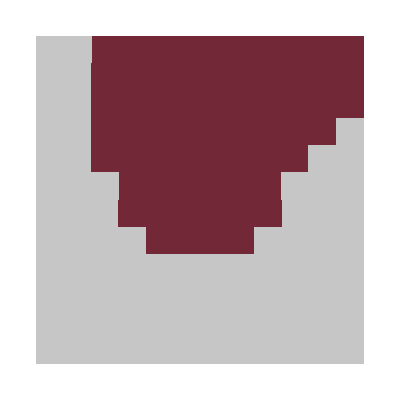
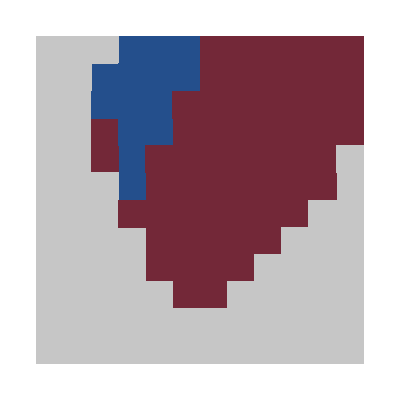
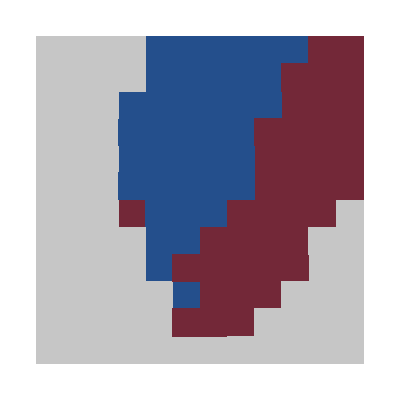
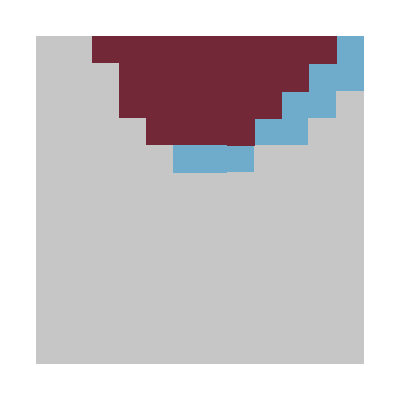
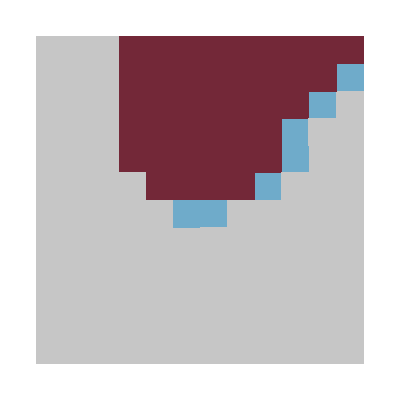
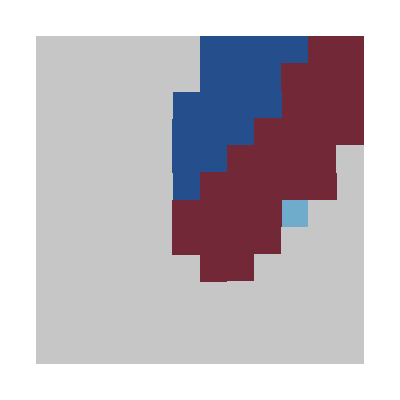
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
DdDde = 0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.05 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["DdDde = "<>ToString[#,TraditionalForm],Black]&/@{0.01,0.05,0.1}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[Flatten/@data,Im@#[[3]]==1&],(*HSS*)
{Log10[4#[[1]]],Log10[4#[[2]]],0}&/@Select[Flatten/@data,Im@#[[3]]==5&],(*TW*)
{Log10[4#[[1]]],Log10[4#[[2]]],1}&/@Select[Flatten/@data,Im@#[[3]]==6&],(*SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],0.8}&/@Select[Flatten/@data,Im@#[[3]]==4&],(*inverted SW*)
{Log10[4#[[1]]],Log10[4#[[2]]],-3}&/@Select[Flatten/@data,Im@#[[3]]==2&](*too short time window*)
],
InterpolationOrder->0,
ColorFunction->(If[#==-4,Darker@Gray,If[#==-3,White,If[#==-2,Darker@Darker@Green,If[#>=0,ColorData["RedBlueTones"][#],Lighter@Lighter@Gray]]]]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
FrameTicks->None,
Frame->None
]
]]/@Reverse@#&)/@analysisListMorphDdDdeFull
]
]
]
```

### Pattern kymographs

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-DdDde_"<>toString[0.01]<>"-kdD_"<>toString[kdD/.params]<>".h5";
data=dataKymo[{filenameT
},{10^4.2/4,10^4.2/4}];
ListDensityPlot[Total@data[[{1,2},-1000;;;;3]],ColorFunction->GrayLevel,InterpolationOrder->0,AspectRatio->3,PlotLegends->Automatic]
```

/rhoD=3962.23,rhoE=3962.23

-Graphics-

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-DdDde_"<>toString[0.01]<>"-kdD_"<>toString[kdD/.params]<>".h5";
data=dataKymo[{filenameT
},{10^3/4,10^4/4}];
ListDensityPlot[Total@data[[{1,2},-1000;;;;3]],ColorFunction->GrayLevel,InterpolationOrder->0,AspectRatio->3,PlotLegends->Automatic]
```

/rhoD=250.,rhoE=2500.

-Graphics-

## Wavelength and period analysis

### kD-kdD wavelength sweep

```mathematica
analysisWP=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-kD_"<>toString[kD]<>"-kdD_"<>toString[kdD]<>".h5"
},
analysisSweepMultipleFiles[{filename
},"TimePoints"->Floor[1000/0.3],"BoundaryPoints"->1,"DX"->0.3,"DT"->0.3]
],{kD,(kD/.params)*10^Range[-1,0.5,0.5]},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

#### Wavelength

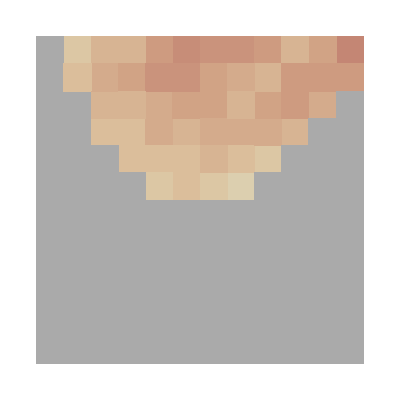
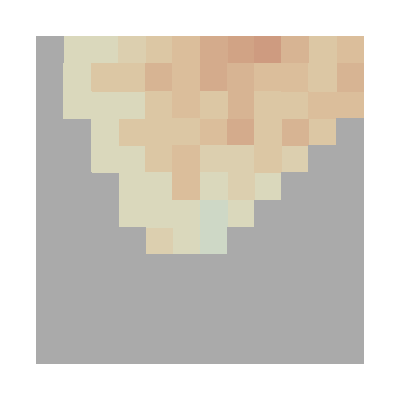
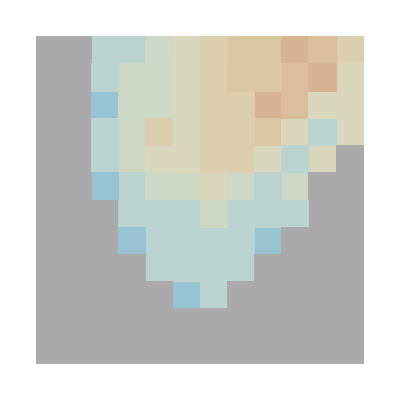
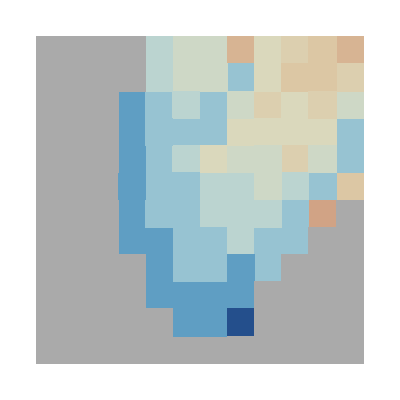
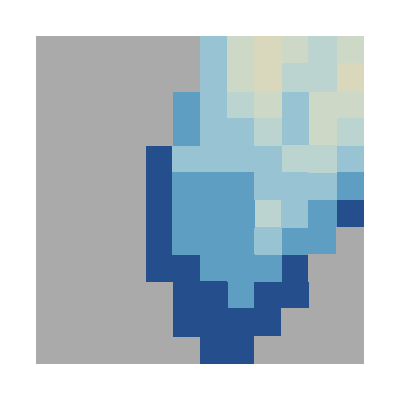
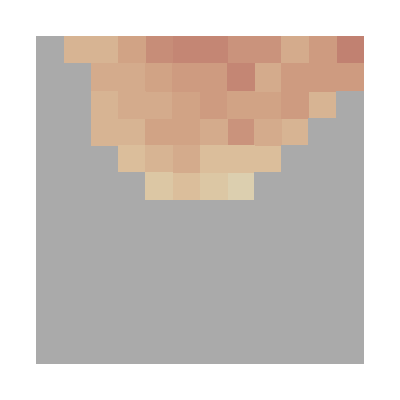
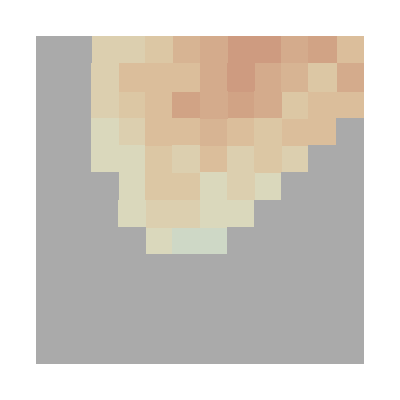
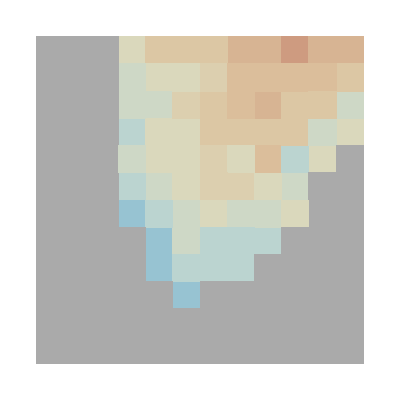
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
0.03 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.0948683 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.3 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
0.948683 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["kD = "<>ToString[#,TraditionalForm],Black]&/@(kD/4/.params)*10^Range[-1,0.5,0.5]]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,2]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWP
]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"switchModel-wavelengthSweep.pdf",
Grid[
Transpose@Join[{Join[{Null},Style["kD = "<>ToString[#,TraditionalForm],Black]&/@(kD/4/.params)*10^Range[-1,0.5,0.5]]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,2]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWP
]
]
]
];
```

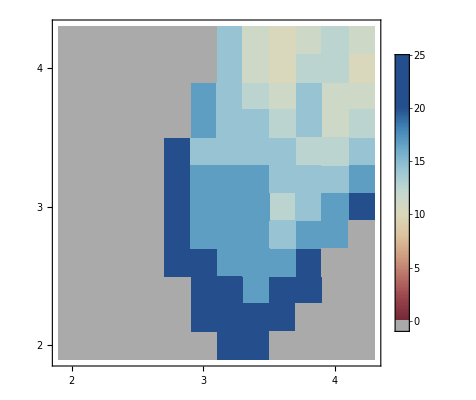

```mathematica
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[analysisWP[[1,1]],Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,2]]}&/@Select[analysisWP[[1,1]],ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3}},
AspectRatio->1,
FrameTicks->{{2,3,4},{2,3,4}},
PlotLegends->Automatic]
```

### kde-kdD sweeps

```mathematica
analysisWPkde=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-kde_"<>toString[kde]<>"-kdD_"<>toString[kdD]<>".h5"
},
analysisSweepMultipleFiles[{filename
},"TimePoints"->500,"BoundaryPoints"->1,"DX"->0.1,"DT"->2]
],{kde,{0.1,2}},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

```mathematica
analysisWPkdeFull={analysisWPkde[[1]],analysisWP[[3]],analysisWPkde[[2]]};
```

#### Wavelength (not included in the article)

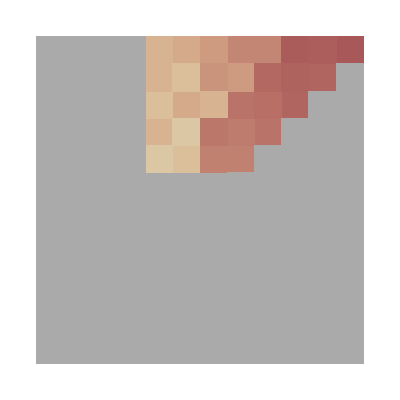
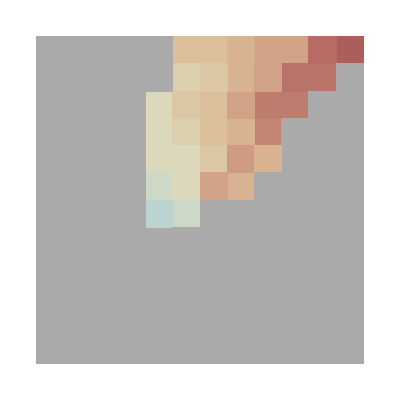
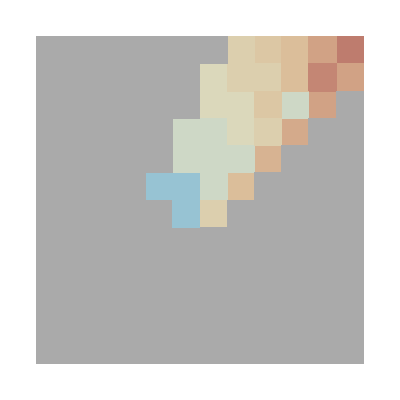
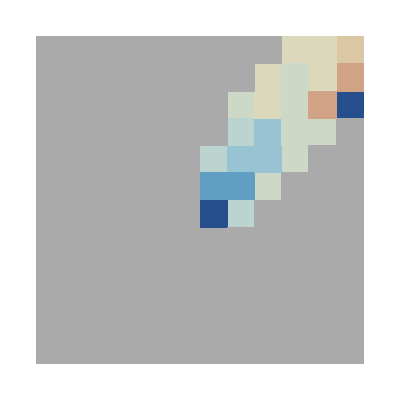
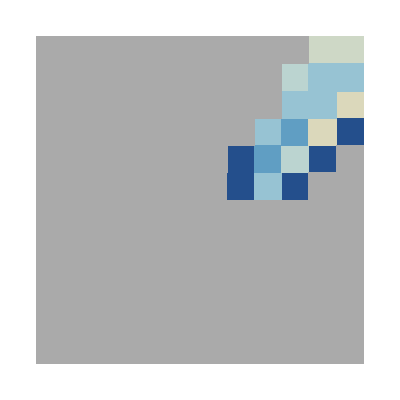
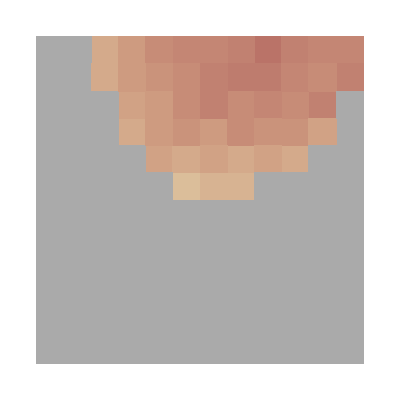
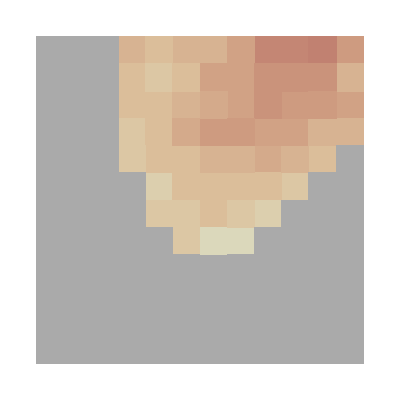
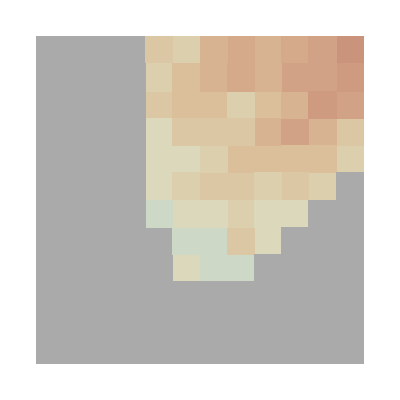
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
kde = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kde = 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kde = 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["kde = "<>ToString[#,TraditionalForm],Black]&/@{0.1,1,2}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,2]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWPkdeFull
]
]
]
```

#### Period

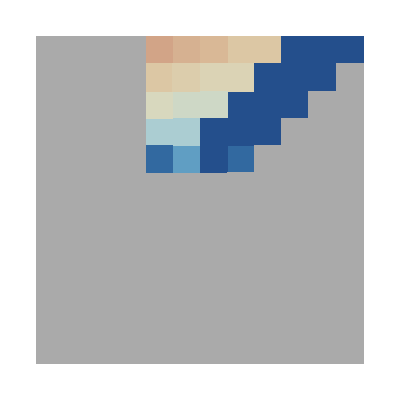
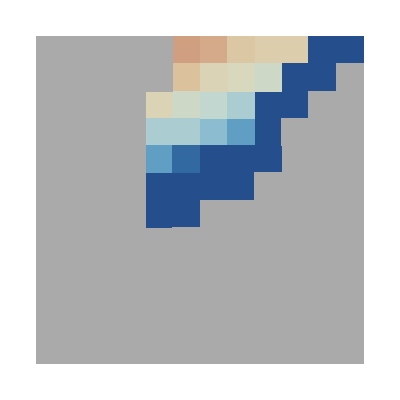
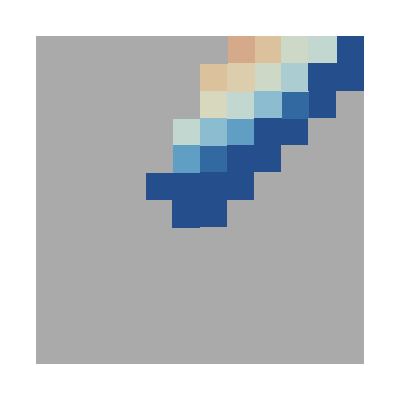
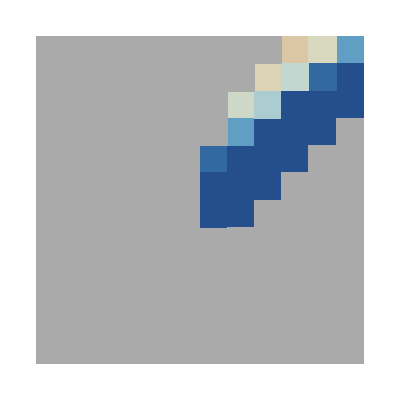
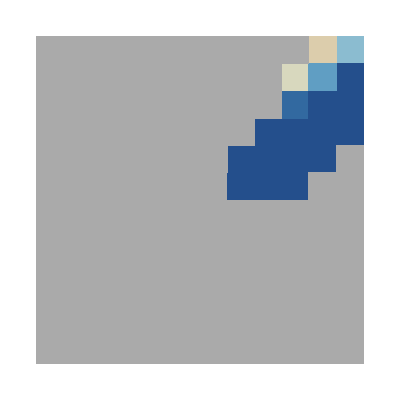
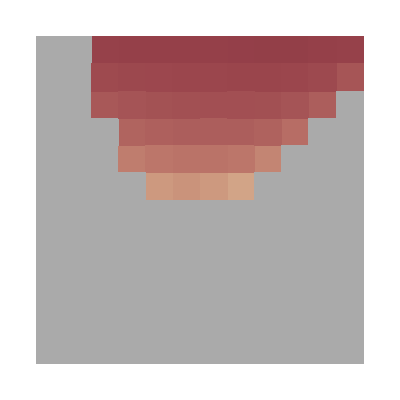
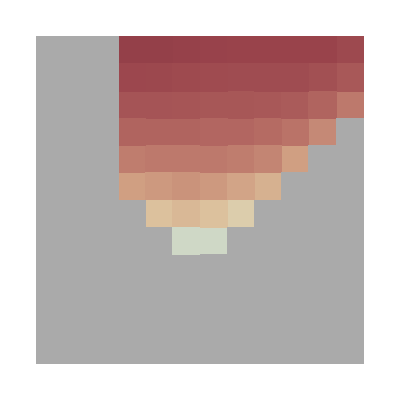
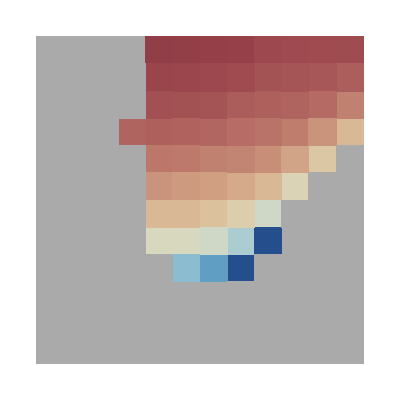
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
kde = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kde = 1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
kde = 2 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["kde = "<>ToString[#,TraditionalForm],Black]&/@{0.1,1,2}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,3]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/150],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWPkdeFull
]
]
]
```

```mathematica
Export[NotebookDirectory[]<>"switchModel-periodSweep.pdf",
Grid[
Transpose@Join[{Join[{Null},Style["kde = "<>ToString[#,TraditionalForm],Black]&/@{0.1,1,2}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,3]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/150],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWPkdeFull
]
]
]
];
```

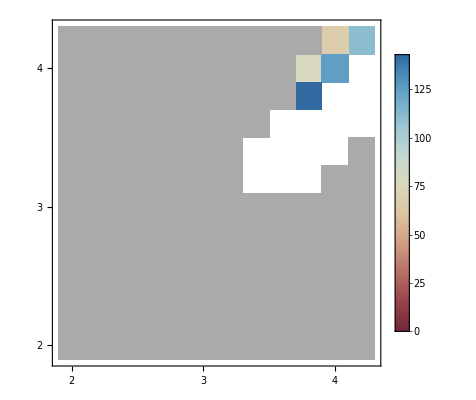

```mathematica
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[analysisWPkdeFull[[1,1]],Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,3]]}&/@Select[analysisWPkdeFull[[1,1]],ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/150],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},{-1,150}},
AspectRatio->1,
FrameTicks->{{2,3,4},{2,3,4}},
PlotLegends->Automatic]
```

#### Jump in oscillation period at kde=2 (not included in the article)

/rhoD=2500.,rhoE=1577.39

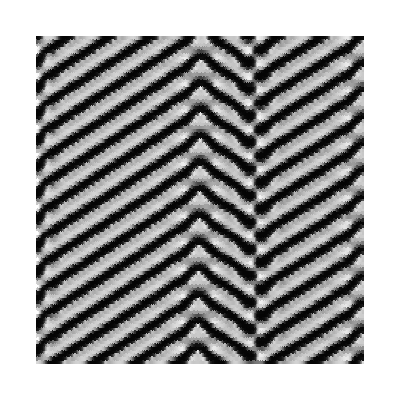

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-kde_"<>toString[2]<>"-kdD_"<>toString[kdD*10/.params]<>".h5";
data=dataKymo[{filenameT
},{10^4/4,10^3.8/4}];
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^4/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

/rhoD=2500.,rhoE=2500.

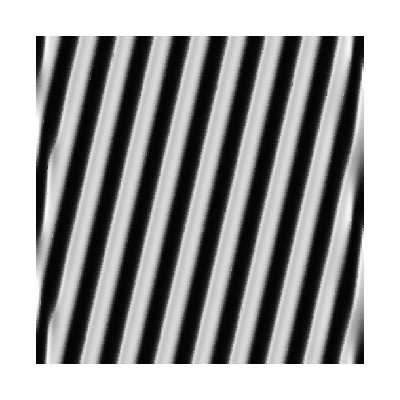

```mathematica
filenameT=NotebookDirectory[]<>"data\\switchModel-1D-rhoDrhoESweep-TA_"<>ToString[T/.params]<>"-kde_"<>toString[2]<>"-kdD_"<>toString[kdD*10/.params]<>".h5";
data=dataKymo[{filenameT
},{10^4/4,10^4/4}];
ListDensityPlot[Total@data[[{1,2},-100;;]],InterpolationOrder->0,AspectRatio->1,ColorFunction->(GrayLevel[#/(2*10^4/4)]&),
ColorFunctionScaling->False,
Frame->None]
```

### DdDde-kdD sweep (not included in the article)

```mathematica
analysisWPDdDde=Table[Block[{filename=NotebookDirectory[]<>"data/switchModel-1D-rhoDrhoESweep-fine-TA_"<>ToString[T/.params]<>"-DdDde_"<>toString[DdDde]<>"-kdD_"<>toString[kdD]<>".h5"
},
analysisSweepMultipleFiles[{filename
},"TimePoints"->Floor[1000/0.3],"BoundaryPoints"->1,"DX"->0.3,"DT"->0.3]
],{DdDde,{0.01,0.1}},{kdD,(kdD/.params)*10^Range[-0.5,1.5,0.5]}];
```

```mathematica
analysisWPDdDdeFull={analysisWPDdDde[[1]],analysisWP[[3]],analysisWPDdDde[[2]]};
```

#### Wavelength

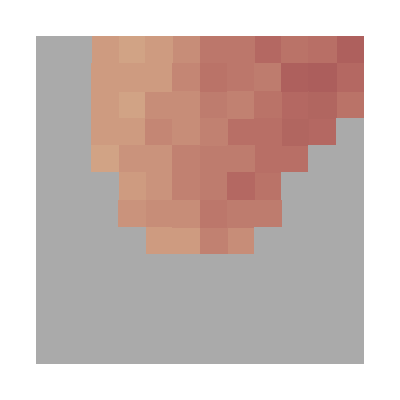
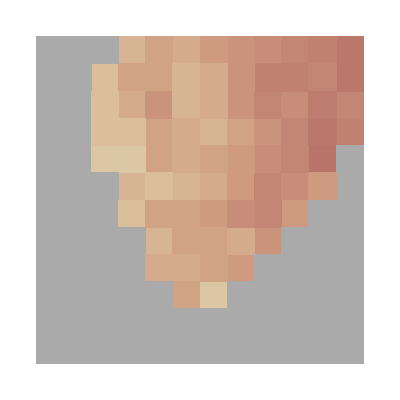
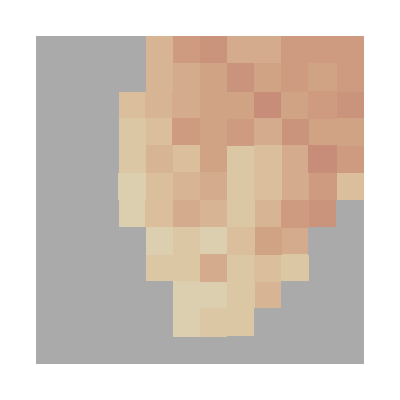
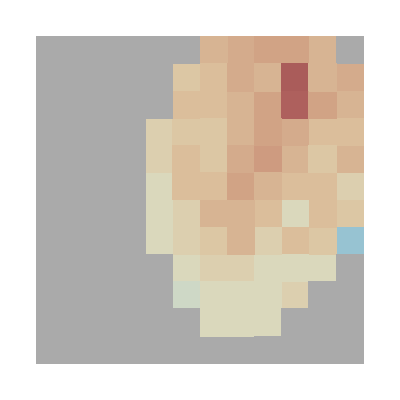
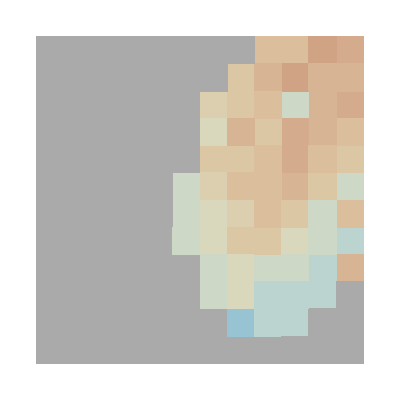
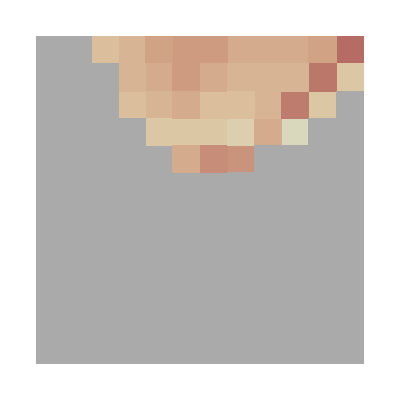
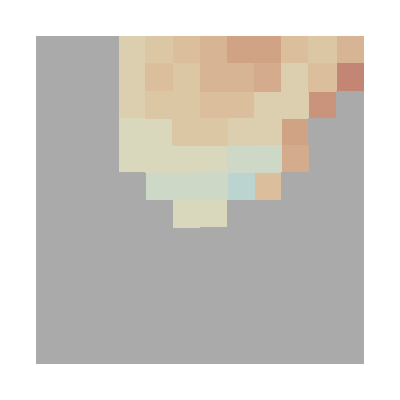
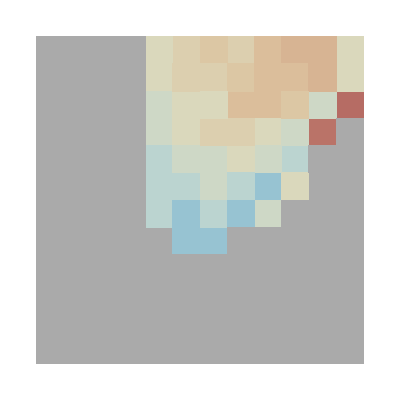
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
DdDde = 0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.05 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["DdDde = "<>ToString[#,TraditionalForm],Black]&/@{0.01,0.05,0.1}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,2]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/20],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWPDdDdeFull
]
]
]
```

#### Period

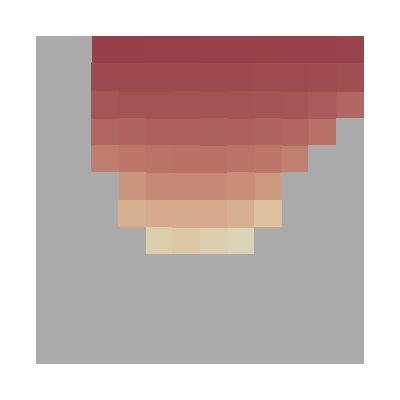
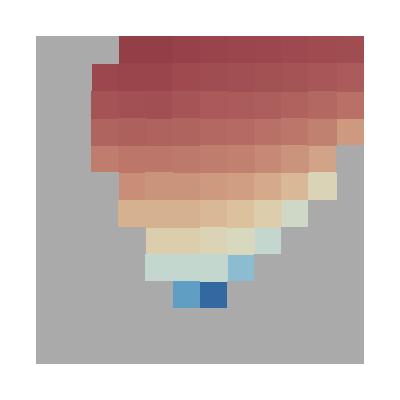
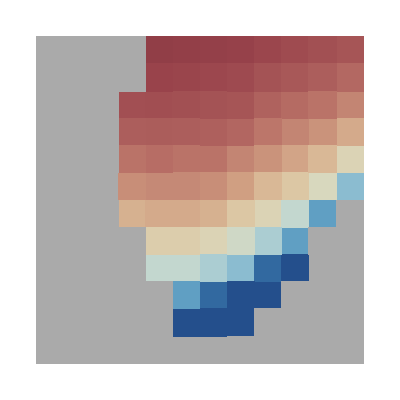
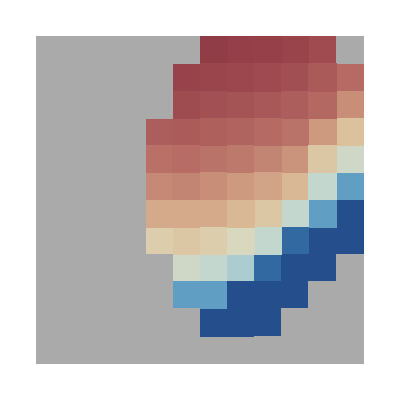
| kdD = 0.0474342 | kdD = 0.015 | kdD = 0.00474342 | kdD = 0.0015 | kdD = 0.000474342
DdDde = 0.01 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.05 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
DdDde = 0.1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose@Join[{Join[{Null},Style["DdDde = "<>ToString[#,TraditionalForm],Black]&/@{0.01,0.05,0.1}]},Transpose@
Join[
{Style["kdD = "<>ToString[#,TraditionalForm],Black]&/@Reverse@((kdD/4/.params)*10^Range[-0.5,1.5,0.5])},

(Function[data,Show[
ListDensityPlot[Join[
{Log10[4#[[1]]],Log10[4#[[2]]],-1}&/@Select[data,Im@#[[3]]!=0&],
{Log10[4#[[1]]],Log10[4#[[2]]],#[[3,3]]}&/@Select[data,ListQ[#[[3]]]&&Im@#[[3,1]]==0&]
],
InterpolationOrder->0,
ColorFunction->(If[#>=0,ColorData["RedBlueTones"][#/150],Lighter@Gray]&),
ColorFunctionScaling->False,
PlotRange->{{1.9,4.3},{1.9,4.3},All},
AspectRatio->1,
Frame->None]
]]/@Reverse@#&)/@analysisWPDdDdeFull
]
]
]
```